### Equations (no mutations to resistance)

Let A and B be the driven alleles at the two loci with initial gamete frequencies:
	x[1]	ab
	x[2]	aB
	x[4]	Ab
	x[5]	AB
That is, a and b are equivalent to your Aw and Bw, while A and B are equivalent to your Ad and Bd.

```mathematica
geno=Transpose[{{x[1],x[2],x[4],x[5]}}].{{x[1],x[2],x[4],x[5]}};
%//MatrixForm
```

(x[1]^2 | x[1] x[2] | x[1] x[4] | x[1] x[5]
x[1] x[2] | x[2]^2 | x[2] x[4] | x[2] x[5]
x[1] x[4] | x[2] x[4] | x[4]^2 | x[4] x[5]
x[1] x[5] | x[2] x[5] | x[4] x[5] | x[5]^2)

A and B both produce a toxin and an antidote to the other toxin. Any individual that produces a toxin without an antidote has fitness ϵ:

```mathematica
fitT={{1,ϵ,ϵ,1},{ϵ,ϵ,1,1},{ϵ,1,ϵ,1},{1,1,1,1}};
%//MatrixForm
```

(1 | ϵ | ϵ | 1
ϵ | ϵ | 1 | 1
ϵ | 1 | ϵ | 1
1 | 1 | 1 | 1)

In addition, we assume that the A drive has a payload that reduces its fitness by √(1-s) in heterozygotes and 1-s in homozygotes if the individual also carries B:

```mathematica
fitP={{1,1,1,√(1-s)},{1,1,√(1-s),√(1-s)},{1,√(1-s),1,1-s},{√(1-s),√(1-s),1-s,1-s}};
%//MatrixForm
```

(1 | 1 | 1 | √(1-s)
1 | 1 | √(1-s) | √(1-s)
1 | √(1-s) | 1 | 1-s
√(1-s) | √(1-s) | 1-s | 1-s)

Freek, I think this matches your fitness matrix and that of Dhole et al.  I’m a little puzzled about why the fitness depends on having the drive allele at the B locus, as seen in your code:

For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],"Bd"]&&MemberQ[Flatten[Genotypes[[i]]],"Ad"],
 W[[i]]=(1-s)^(1/2);If[Count[Flatten[Genotypes[[i]]],"Ad"]==2,W[[i]]=(1-s)]
]
]

OH - I get it.  For the payload, Dhole et al. really assume the following fitness matrix due to the payload alone (there is no dependence on locus B)...it is when this matrix is multiplied by the ϵ=0 that the other terms go away.  So we should use this fitness matrix for a payload at locus A only:

(1 | 1 | √(1-s) | √(1-s)
1 | 1 | √(1-s) | √(1-s)
√(1-s) | √(1-s) | 1-s | 1-s
√(1-s) | √(1-s) | 1-s | 1-s)

Or we could allow two independent payloads at locus A and B:

fitPA={{1,1,√(1-sA),√(1-sA)},{1,1,√(1-sA),√(1-sA)},{√(1-sA),√(1-sA),1-sA,1-sA},{√(1-sA),√(1-sA),1-sA,1-sA}};
fitPB = {{1,√(1-sB),1,√(1-sB)},{√(1-sB),1-sB,√(1-sB),1-sB},{1,√(1-sB),1,√(1-sB)},{√(1-sB),1-sB,√(1-sB),1-sB}};

Or we could assume the same payload gene is attached to both, but then we would need to consider how they interact epistatically.

For now, I’ve just corrected the payload at locus A only to match what Dhole et al. meant (if we could see behind their zeros in Table 2):

```mathematica
fitP={{1,1,√(1-s),√(1-s)},{1,1,√(1-s),√(1-s)},{√(1-s),√(1-s),1-s,1-s},{√(1-s),√(1-s),1-s,1-s}};
%//MatrixForm
```

(1 | 1 | √(1-s) | √(1-s)
1 | 1 | √(1-s) | √(1-s)
√(1-s) | √(1-s) | 1-s | 1-s
√(1-s) | √(1-s) | 1-s | 1-s)

```mathematica
fitP=fitP/.√(1-s)->1-h s;
```

I prefer to avoid the squareroots for the purposes of simplification, so I used 1-h s instead, which allows any form of dominance in the payload cost and so is more general.

We assume that these two fitness effects are multiplicative to give the total fitness:

```mathematica
fitT fitP//Flatten
```

{1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s}

The mean fitness is:

```mathematica
Total[fitT fitP*geno,2]
```

x[1]^2+2 ϵ x[1] x[2]+ϵ x[2]^2+2 (1-h s) ϵ x[1] x[4]+2 (1-h s) x[2] x[4]+(1-s) ϵ x[4]^2+2 (1-h s) x[1] x[5]+2 (1-h s) x[2] x[5]+2 (1-s) x[4] x[5]+(1-s) x[5]^2

We next model drive and recombination, allowing recombination at arbitrary rate r (set to 1/2 in Freek’s code).

The gametes of x[1] x[4] individuals will undergo drive first at each locus:
	(1-d)^2 no drive (ab/AB then recombines)
	(1-d)d drive at locus B only (giving aB/AB)
	d(1-d) drive at locus A only (giving Ab/AB)
	d^2 drive at both loci (giving AB/AB)
yielding the following total gamete frequencies:

```mathematica
type15={(1-d)^2(1-r)/2,(1-d)^2 r/2,(1-d)^2 r/2,(1-d)^2(1-r)/2}+{0,(1-d)d 1/2,0,(1-d)d 1/2}+{0,0,d(1-d)1/2,d(1-d)1/2}+{0,0,0,d^2};
```

This correctly simplifies when drive is absent or complete:

```mathematica
type15/.d->0//Factor
type15/.d->1//Factor
```

{(1-r)/2,r/2,r/2,(1-r)/2}

{0,0,0,1}

```mathematica
Total[type15]//Factor
```

1

The gametes of x[2] x[4] individuals will undergo drive first at each locus:
	(1-d)^2 no drive (aB/Ab then recombines)
	(1-d)d drive at locus B only (giving aB/AB)
	d(1-d) drive at locus A only (giving AB/Ab)
	d^2 drive at both loci (giving AB/AB)
yielding the following total gamete frequencies:

```mathematica
type24={(1-d)^2 r/2,(1-d)^2(1-r)/2,(1-d)^2(1-r)/2,(1-d)^2 r/2}+{0,(1-d)d 1/2,0,(1-d)d 1/2}+{0,0,d(1-d)1/2,d(1-d)1/2}+{0,0,0,d^2};
```

```mathematica
Total[type24]//Factor
```

1

Altogether, the matrix of gamete types produced by each diploid genotype is:

```mathematica
seg={{{1,0,0,0},{(1-d)/2,(1+d)/2,0,0},{(1-d)/2,0,(1+d)/2,0},type15},
{{(1-d)/2,(1+d)/2,0,0},{0,1,0,0},type24,{0,(1-d)/2,0,(1+d)/2}},
{{(1-d)/2,0,(1+d)/2,0},type24,{0,0,1,0},{0,0,(1-d)/2,(1+d)/2}},
{type15,{0,(1-d)/2,0,(1+d)/2},{0,0,(1-d)/2,(1+d)/2},{0,0,0,1}}};
```

```mathematica
Table[Sum[seg[[i,j,k]],{k,1,4}],{i,1,4},{j,1,4}]//Factor
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

Applying selection and then meiosis gives the matrix of gametes produced by each type in the next generation:

```mathematica
newgen=((fitT*fitP*geno)/Total[fitT*fitP*geno,2]*seg)//Factor;
```

```mathematica
newgen;
```

Summing across all individuals, we get the next generation of gametes:

```mathematica
newgametes=Table[Sum[newgen[[i,j,k]],{i,1,4},{j,1,4}],{k,1,4}];
```

```mathematica
newgametes[[1]]//Simplify
```

(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))

Freek, this is much simpler than the eq terms that you sent me, and I cannot recreate your equations even with different orders of events.  Am I assuming something different in deriving the equations or did something go haywire in your derivations?  I’ve also tried changing drive, because I think you assumed that with probability d all loci would be driven in double heterozygotes, 

type15={(1-d)(1-r)/2,(1-d)r/2,(1-d)r/2,(1-d)(1-r)/2}+{0,0,0,d};
type24={(1-d)r/2,(1-d)(1-r)/2,(1-d)(1-r)/2,(1-d)r/2}+{0,0,0,d};

Some checks:

```mathematica
subx={x[1]->(1-pA)(1- pB) + dis,x[2]->(1-pA) pB  - dis,x[4]->pA (1-pB)-dis,x[5]->pA pB  + dis};
```

In the absence of selection, this correctly gives the genotype frequency dynamics with recombination:

```mathematica
Collect[Factor[newgametes/.s->0/.d->0/.ϵ->1/.subx],dis,Factor]
```

{(-1+pA) (-1+pB)+dis (1-r),-(-1+pA) pB+dis (-1+r),-pA (-1+pB)+dis (-1+r),pA pB+dis (1-r)}

With only drive, the allele frequencies are driven at each locus independently and change in frequency as if there were selection acting with strength d:

```mathematica
Collect[Factor[newgametes[[1]]+newgametes[[2]]-(1-pA)/.s->0/.ϵ->1/.subx],dis,Factor]
```

d (-1+pA) pA

```mathematica
Collect[Factor[newgametes[[1]]+newgametes[[3]]-(1-pB)/.s->0/.ϵ->1/.subx],dis,Factor]
```

d (-1+pB) pB

And the disequilibrium in the next generation is zero if it starts at zero (drive is independent at the two loci and does not generate disequilibrium):

```mathematica
Factor[newgametes[[1]]*newgametes[[4]]-newgametes[[2]]*newgametes[[3]]/.s->0/.ϵ->1/.subx/.dis->0]
```

0

### Critical value of recombination rate that allows invasion

We first ask when drive can get in, assuming that fitnesses are so low for Ab or aB that they could not invade (e.g., ϵ = 0).  Allowing any recombination rate, tight enough linkage will allow invasion of AB into a population fixed for ab:

```mathematica
mat={{D[newgametes[[2]],x[2]],D[newgametes[[2]],x[4]],D[newgametes[[2]],x[5]]},
{D[newgametes[[3]],x[2]],D[newgametes[[3]],x[4]],D[newgametes[[3]],x[5]]},
{D[newgametes[[4]],x[2]],D[newgametes[[4]],x[4]],D[newgametes[[4]],x[5]]}}/.x[1]->1/.x[2]->0/.x[4]->0/.x[5]->0;
```

```mathematica
mat//Factor//MatrixForm
```

((1+d) ϵ | 0 | -(-1+d) (-d-r+d r) (-1+h s)
0 | -(1+d) (-1+h s) ϵ | -(-1+d) (-d-r+d r) (-1+h s)
0 | 0 | (-1-d^2+r-2 d r+d^2 r) (-1+h s))

```mathematica
Eigenvalues[({{(1+d) ϵ, 0, -(-1+d) (-d-r+d r) (-1+h s)}, {0, -(1+d) (-1+h s) ϵ, -(-1+d) (-d-r+d r) (-1+h s)}, {0, 0, (-1-d^2+r-2 d r+d^2 r) (-1+h s)}})]/.r->1/2//Simplify
```

{-1/2 (1+d)^2 (-1+h s),(1+d) ϵ,-(1+d) (-1+h s) ϵ}

The eigenvalues of which are (1+d) ϵ and (1+d) ϵ (1-h s) for the invasion of aB or Ab, respectively, and (-1-d^2+r-2 d r+d^2 r) (-1+h s) for the invasion of AB.  
We assume that ϵ is small enough that (1+d) ϵ<1 and neither Ab nor aB can invade on their own.  
Nevertheless, AB can invade when rare if recombination is lower than:

```mathematica
critr=Solve[mat[[3,3]]==1,r]//Simplify//Flatten
```

{r→(h s+d^2 (-1+h s))/((-1+d)^2 (-1+h s))}

Invasion occurs in the shaded regions (r small enough, d large enough, hs small enough)

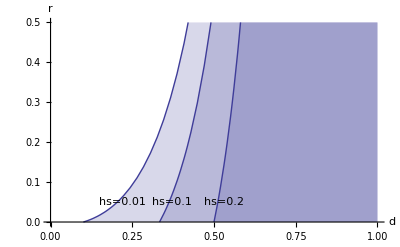

```mathematica
Show[
Plot[(d^2 (1-h s)-h s)/((1-d)^2 (1-h s))/.h s ->{0.01,0.1,0.2},{d,0,1},PlotRange->{Automatic,{0,0.5}},Filling->Bottom,AxesLabel->{"d","r"}],
Graphics[Text["hs=0.01",{0.22,0.05}]],
Graphics[Text["hs=0.1",{0.37,0.05}]],
Graphics[Text["hs=0.2",{0.53,0.05}]]
]
```

If r = 1/2 and 1-hs = √(1-s), we need s to be weaker than:

```mathematica
Solve[(mat[[3,3]]/.r->1/2/. h s -> 1-√(1-s))==1,s]//Simplify//Flatten
```

{s→(-3+4 d+6 d^2+4 d^3+d^4)/(1+d)^4}

which equals 1-4/(1+d)^4allowing invasion in the shaded region, even for very small initial frequencies of AB:

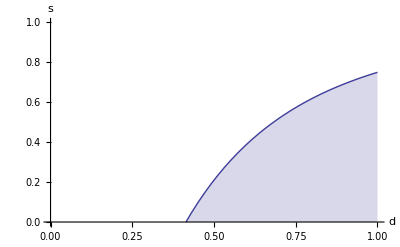

```mathematica
Plot[1-4/(1+d)^4,{d,0,1},PlotRange->{Automatic,{0,1}},Filling->Bottom,AxesLabel->{"d","s"}]
```

In the following, we assume that AB cannot invade when rare and ask if there is a frequency of AB above which invasion is assured.

### Equilibrium analysis - general case

Working in terms of pA, pB, and dis, the following three equations must equal zero at an equilibrium:

```mathematica
term1=newgametes[[1]]+newgametes[[2]]-(1-pA)/.subx//Factor//Numerator
```

-dis-d dis-d dis^2+pA+4 dis pA+2 d dis pA+2 dis^2 pA-2 pA^2-4 dis pA^2+pA^3+dis pB+d dis pB-4 pA pB-2 d pA pB-4 dis pA pB-2 d dis pA pB+8 pA^2 pB+2 d pA^2 pB+4 dis pA^2 pB-4 pA^3 pB+2 pA pB^2+d pA pB^2-4 pA^2 pB^2-d pA^2 pB^2+2 pA^3 pB^2-dis^2 s+dis h s+d dis h s+dis^2 h s+d dis^2 h s+2 dis pA s+dis^2 pA s-4 dis h pA s-2 d dis h pA s-2 dis^2 h pA s-2 dis pA^2 s+4 dis h pA^2 s-dis h pB s-d dis h pB s-2 dis pA pB s+2 h pA pB s+2 d h pA pB s+4 dis h pA pB s+2 d dis h pA pB s+2 pA^2 pB s+2 dis pA^2 pB s-6 h pA^2 pB s-2 d h pA^2 pB s-4 dis h pA^2 pB s-2 pA^3 pB s+4 h pA^3 pB s-h pA pB^2 s-d h pA pB^2 s-pA^2 pB^2 s+3 h pA^2 pB^2 s+d h pA^2 pB^2 s+pA^3 pB^2 s-2 h pA^3 pB^2 s+dis ϵ+d dis ϵ+d dis^2 ϵ-pA ϵ-d pA ϵ-4 dis pA ϵ-2 d dis pA ϵ-2 dis^2 pA ϵ+2 pA^2 ϵ+d pA^2 ϵ+4 dis pA^2 ϵ-pA^3 ϵ-dis pB ϵ-d dis pB ϵ+4 pA pB ϵ+2 d pA pB ϵ+4 dis pA pB ϵ+2 d dis pA pB ϵ-8 pA^2 pB ϵ-2 d pA^2 pB ϵ-4 dis pA^2 pB ϵ+4 pA^3 pB ϵ-2 pA pB^2 ϵ-d pA pB^2 ϵ+4 pA^2 pB^2 ϵ+d pA^2 pB^2 ϵ-2 pA^3 pB^2 ϵ+dis^2 s ϵ-dis h s ϵ-d dis h s ϵ-dis^2 h s ϵ-d dis^2 h s ϵ-2 dis pA s ϵ-dis^2 pA s ϵ+h pA s ϵ+d h pA s ϵ+4 dis h pA s ϵ+2 d dis h pA s ϵ+2 dis^2 h pA s ϵ+pA^2 s ϵ+2 dis pA^2 s ϵ-3 h pA^2 s ϵ-d h pA^2 s ϵ-4 dis h pA^2 s ϵ-pA^3 s ϵ+2 h pA^3 s ϵ+dis h pB s ϵ+d dis h pB s ϵ+2 dis pA pB s ϵ-2 h pA pB s ϵ-2 d h pA pB s ϵ-4 dis h pA pB s ϵ-2 d dis h pA pB s ϵ-2 pA^2 pB s ϵ-2 dis pA^2 pB s ϵ+6 h pA^2 pB s ϵ+2 d h pA^2 pB s ϵ+4 dis h pA^2 pB s ϵ+2 pA^3 pB s ϵ-4 h pA^3 pB s ϵ+h pA pB^2 s ϵ+d h pA pB^2 s ϵ+pA^2 pB^2 s ϵ-3 h pA^2 pB^2 s ϵ-d h pA^2 pB^2 s ϵ-pA^3 pB^2 s ϵ+2 h pA^3 pB^2 s ϵ

```mathematica
term2=newgametes[[1]]+newgametes[[3]]-(1-pB)/.subx//Factor//Numerator
```

-dis-d dis-d dis^2+dis pA+d dis pA+pB+4 dis pB+2 d dis pB+2 dis^2 pB-4 pA pB-2 d pA pB-4 dis pA pB-2 d dis pA pB+2 pA^2 pB+d pA^2 pB-2 pB^2-4 dis pB^2+8 pA pB^2+2 d pA pB^2+4 dis pA pB^2-4 pA^2 pB^2-d pA^2 pB^2+pB^3-4 pA pB^3+2 pA^2 pB^3-d dis^2 s+dis h s+d dis h s+2 d dis^2 h s+dis pA s+d dis pA s-2 dis h pA s-2 d dis h pA s+dis^2 pB s-2 dis h pB s-2 d dis h pB s-2 dis^2 h pB s-2 dis pA pB s-2 d dis pA pB s+2 h pA pB s+2 d h pA pB s+4 dis h pA pB s+4 d dis h pA pB s+pA^2 pB s+d pA^2 pB s-2 h pA^2 pB s-2 d h pA^2 pB s+2 dis h pB^2 s+2 dis pA pB^2 s-4 h pA pB^2 s-2 d h pA pB^2 s-4 dis h pA pB^2 s-2 pA^2 pB^2 s-d pA^2 pB^2 s+4 h pA^2 pB^2 s+2 d h pA^2 pB^2 s+2 h pA pB^3 s+pA^2 pB^3 s-2 h pA^2 pB^3 s+dis ϵ+d dis ϵ+d dis^2 ϵ-dis pA ϵ-d dis pA ϵ-pB ϵ-d pB ϵ-4 dis pB ϵ-2 d dis pB ϵ-2 dis^2 pB ϵ+4 pA pB ϵ+2 d pA pB ϵ+4 dis pA pB ϵ+2 d dis pA pB ϵ-2 pA^2 pB ϵ-d pA^2 pB ϵ+2 pB^2 ϵ+d pB^2 ϵ+4 dis pB^2 ϵ-8 pA pB^2 ϵ-2 d pA pB^2 ϵ-4 dis pA pB^2 ϵ+4 pA^2 pB^2 ϵ+d pA^2 pB^2 ϵ-pB^3 ϵ+4 pA pB^3 ϵ-2 pA^2 pB^3 ϵ-dis^2 pB s ϵ+2 dis h pB s ϵ+2 dis^2 h pB s ϵ+2 dis pA pB s ϵ-2 h pA pB s ϵ-4 dis h pA pB s ϵ-pA^2 pB s ϵ+2 h pA^2 pB s ϵ-2 dis h pB^2 s ϵ-2 dis pA pB^2 s ϵ+4 h pA pB^2 s ϵ+4 dis h pA pB^2 s ϵ+2 pA^2 pB^2 s ϵ-4 h pA^2 pB^2 s ϵ-2 h pA pB^3 s ϵ-pA^2 pB^3 s ϵ+2 h pA^2 pB^3 s ϵ

```mathematica
term3=newgametes[[1]]*newgametes[[4]]-newgametes[[2]]newgametes[[3]]-dis/.subx//Factor//Numerator
```

d^2 dis-5 dis^2-2 d dis^2+4 d^2 dis^2-18 dis^3-2 d dis^3+4 d^2 dis^3-16 dis^4+d^2 dis^4-4 dis^5+2 dis pA-d dis pA-3 d^2 dis pA+21 dis^2 pA-7 d^2 dis^2 pA+2323+16 dis h^2 pA^2 pB^3 s^2 ϵ^2+24 dis^2 h^2 pA^2 pB^3 s^2 ϵ^2-4 dis^2 pA^3 pB^3 s^2 ϵ^2+16 dis h pA^3 pB^3 s^2 ϵ^2+16 dis^2 h pA^3 pB^3 s^2 ϵ^2-32 dis h^2 pA^3 pB^3 s^2 ϵ^2-16 dis^2 h^2 pA^3 pB^3 s^2 ϵ^2+4 dis pA^4 pB^3 s^2 ϵ^2-16 dis h pA^4 pB^3 s^2 ϵ^2+16 dis h^2 pA^4 pB^3 s^2 ϵ^2-4 dis h^2 pA^2 pB^4 s^2 ϵ^2-4 dis h pA^3 pB^4 s^2 ϵ^2+8 dis h^2 pA^3 pB^4 s^2 ϵ^2-dis pA^4 pB^4 s^2 ϵ^2+4 dis h pA^4 pB^4 s^2 ϵ^2-4 dis h^2 pA^4 pB^4 s^2 ϵ^2
 |  |  |  |

We can solve for the disequilibrium by cancelling out the dis^2 terms in the first two of these equations:

```mathematica
Factor[Coefficient[term2,dis^2] term1-Coefficient[term1,dis^2]term2];
dissol=Flatten[Solve[%==0,dis]]
```

{dis→(d pA-2 d pA^2+d pA^3-d pB-4 pA^2 pB+2 d pA^2 pB+d^2 pA^2 pB+2 pA^3 pB-2 d pA^3 pB+2 d pB^2+4 pA pB^2-2 d pA pB^2-d^2 pA pB^2-d pB^3-2 pA pB^3+2 d pA pB^3+d pA s-2 d h pA s-2 d pA^2 s+4 d h pA^2 s+d pA^3 s-2 d h pA^3 s-pB s+h pB s+d h pB s+4 pA pB s-2 d pA pB s-2 d^2 pA pB s-4 h pA pB s+2 d h pA pB s+2 d^2 h pA pB s-4 pA^2 pB s+6 d pA^2 pB s+d^2 pA^2 pB s+10 h pA^2 pB s-9 d h pA^2 pB s-3 d^2 h pA^2 pB s+3 pA^3 pB s-3 d pA^3 pB s-6 h pA^3 pB s+6 d h pA^3 pB s+2 pB^2 s-2 h pB^2 s-2 d h pB^2 s-6 pA pB^2 s+2 d pA pB^2 s+d^2 pA pB^2 s+d h pA pB^2 s+d^2 h pA pB^2 s-2 d pA^2 pB^2 s+2 d h pA^2 pB^2 s-pB^3 s+h pB^3 s+d h pB^3 s+3 pA pB^3 s-d pA pB^3 s-2 d h pA pB^3 s-2 h pA pB s^2+2 d^2 h pA pB s^2+2 h^2 pA pB s^2-2 d^2 h^2 pA pB s^2-pA^2 pB s^2+d pA^2 pB s^2+5 h pA^2 pB s^2-4 d h pA^2 pB s^2-d^2 h pA^2 pB s^2-6 h^2 pA^2 pB s^2+4 d h^2 pA^2 pB s^2+2 d^2 h^2 pA^2 pB s^2+pA^3 pB s^2-d pA^3 pB s^2-4 h pA^3 pB s^2+4 d h pA^3 pB s^2+4 h^2 pA^3 pB s^2-4 d h^2 pA^3 pB s^2+2 h pA pB^2 s^2-d h pA pB^2 s^2-d^2 h pA pB^2 s^2-h pA pB^3 s^2+d h pA pB^3 s^2-2 d pA ϵ-d^2 pA ϵ+4 d pA^2 ϵ+d^2 pA^2 ϵ-2 d pA^3 ϵ+2 d pB ϵ+d^2 pB ϵ+8 pA^2 pB ϵ-6 d pA^2 pB ϵ-2 d^2 pA^2 pB ϵ-4 pA^3 pB ϵ+4 d pA^3 pB ϵ-4 d pB^2 ϵ-d^2 pB^2 ϵ-8 pA pB^2 ϵ+6 d pA pB^2 ϵ+2 d^2 pA pB^2 ϵ+2 d pB^3 ϵ+4 pA pB^3 ϵ-4 d pA pB^3 ϵ-d pA s ϵ-d^2 pA s ϵ+3 d h pA s ϵ+3 d^2 h pA s ϵ+3 d pA^2 s ϵ+d^2 pA^2 s ϵ-7 d h pA^2 s ϵ-3 d^2 h pA^2 s ϵ-2 d pA^3 s ϵ+4 d h pA^3 s ϵ+2 pB s ϵ+d pB s ϵ-2 h pB s ϵ-3 d h pB s ϵ-d^2 h pB s ϵ-8 pA pB s ϵ+2 d^2 pA pB s ϵ+6 h pA pB s ϵ+2 d h pA pB s ϵ-2 d^2 h pA pB s ϵ+6 pA^2 pB s ϵ-5 d pA^2 pB s ϵ-d^2 pA^2 pB s ϵ-14 h pA^2 pB s ϵ+10 d h pA^2 pB s ϵ+4 d^2 h pA^2 pB s ϵ-4 pA^3 pB s ϵ+4 d pA^3 pB s ϵ+8 h pA^3 pB s ϵ-8 d h pA^3 pB s ϵ-4 pB^2 s ϵ-d pB^2 s ϵ+4 h pB^2 s ϵ+5 d h pB^2 s ϵ+d^2 h pB^2 s ϵ+12 pA pB^2 s ϵ-d pA pB^2 s ϵ-d^2 pA pB^2 s ϵ-8 d h pA pB^2 s ϵ-2 d^2 h pA pB^2 s ϵ+2 pB^3 s ϵ-2 h pB^3 s ϵ-2 d h pB^3 s ϵ-6 pA pB^3 s ϵ+2 d pA pB^3 s ϵ+4 d h pA pB^3 s ϵ+d h pA s^2 ϵ+d^2 h pA s^2 ϵ-2 d h^2 pA s^2 ϵ-2 d^2 h^2 pA s^2 ϵ+d pA^2 s^2 ϵ-5 d h pA^2 s^2 ϵ-d^2 h pA^2 s^2 ϵ+6 d h^2 pA^2 s^2 ϵ+2 d^2 h^2 pA^2 s^2 ϵ-d pA^3 s^2 ϵ+4 d h pA^3 s^2 ϵ-4 d h^2 pA^3 s^2 ϵ+3 h pA pB s^2 ϵ-d h pA pB s^2 ϵ-2 d^2 h pA pB s^2 ϵ-2 h^2 pA pB s^2 ϵ+2 d^2 h^2 pA pB s^2 ϵ+pA^2 pB s^2 ϵ-d pA^2 pB s^2 ϵ-5 h pA^2 pB s^2 ϵ+4 d h pA^2 pB s^2 ϵ+d^2 h pA^2 pB s^2 ϵ+6 h^2 pA^2 pB s^2 ϵ-4 d h^2 pA^2 pB s^2 ϵ-2 d^2 h^2 pA^2 pB s^2 ϵ-pA^3 pB s^2 ϵ+d pA^3 pB s^2 ϵ+4 h pA^3 pB s^2 ϵ-4 d h pA^3 pB s^2 ϵ-4 h^2 pA^3 pB s^2 ϵ+4 d h^2 pA^3 pB s^2 ϵ-4 h pA pB^2 s^2 ϵ+3 d h pA pB^2 s^2 ϵ+d^2 h pA pB^2 s^2 ϵ+2 h pA pB^3 s^2 ϵ-2 d h pA pB^3 s^2 ϵ+d pA ϵ^2+d^2 pA ϵ^2-2 d pA^2 ϵ^2-d^2 pA^2 ϵ^2+d pA^3 ϵ^2-d pB ϵ^2-d^2 pB ϵ^2-4 pA^2 pB ϵ^2+4 d pA^2 pB ϵ^2+d^2 pA^2 pB ϵ^2+2 pA^3 pB ϵ^2-2 d pA^3 pB ϵ^2+2 d pB^2 ϵ^2+d^2 pB^2 ϵ^2+4 pA pB^2 ϵ^2-4 d pA pB^2 ϵ^2-d^2 pA pB^2 ϵ^2-d pB^3 ϵ^2-2 pA pB^3 ϵ^2+2 d pA pB^3 ϵ^2-d h pA s ϵ^2-d^2 h pA s ϵ^2-d pA^2 s ϵ^2+3 d h pA^2 s ϵ^2+d^2 h pA^2 s ϵ^2+d pA^3 s ϵ^2-2 d h pA^3 s ϵ^2-pB s ϵ^2-d pB s ϵ^2+h pB s ϵ^2+2 d h pB s ϵ^2+d^2 h pB s ϵ^2+4 pA pB s ϵ^2+2 d pA pB s ϵ^2-2 h pA pB s ϵ^2-4 d h pA pB s ϵ^2-2 pA^2 pB s ϵ^2-d pA^2 pB s ϵ^2+4 h pA^2 pB s ϵ^2-d h pA^2 pB s ϵ^2-d^2 h pA^2 pB s ϵ^2+pA^3 pB s ϵ^2-d pA^3 pB s ϵ^2-2 h pA^3 pB s ϵ^2+2 d h pA^3 pB s ϵ^2+2 pB^2 s ϵ^2+d pB^2 s ϵ^2-2 h pB^2 s ϵ^2-3 d h pB^2 s ϵ^2-d^2 h pB^2 s ϵ^2-6 pA pB^2 s ϵ^2-d pA pB^2 s ϵ^2+7 d h pA pB^2 s ϵ^2+d^2 h pA pB^2 s ϵ^2+2 d pA^2 pB^2 s ϵ^2-2 d h pA^2 pB^2 s ϵ^2-pB^3 s ϵ^2+h pB^3 s ϵ^2+d h pB^3 s ϵ^2+3 pA pB^3 s ϵ^2-d pA pB^3 s ϵ^2-2 d h pA pB^3 s ϵ^2-h pA pB s^2 ϵ^2+d h pA pB s^2 ϵ^2+2 h pA pB^2 s^2 ϵ^2-2 d h pA pB^2 s^2 ϵ^2-h pA pB^3 s^2 ϵ^2+d h pA pB^3 s^2 ϵ^2)/(2 pA-d pA-d^2 pA-2 pA^2+2 d pA^2-2 pB+d pB+d^2 pB+2 pB^2-2 d pB^2-s+d^2 s+h s-d^2 h s+2 pA s-3 d pA s-d^2 pA s-5 h pA s+4 d h pA s+3 d^2 h pA s-3 pA^2 s+3 d pA^2 s+6 h pA^2 s-6 d h pA^2 s+3 pB s-d^2 pB s-d h pB s-d^2 h pB s+2 d pA pB s-2 d h pA pB s-3 pB^2 s+d pB^2 s+2 d h pB^2 s+h s^2-d^2 h s^2-h^2 s^2+d^2 h^2 s^2+pA s^2-d pA s^2-4 h pA s^2+3 d h pA s^2+d^2 h pA s^2+4 h^2 pA s^2-2 d h^2 pA s^2-2 d^2 h^2 pA s^2-pA^2 s^2+d pA^2 s^2+4 h pA^2 s^2-4 d h pA^2 s^2-4 h^2 pA^2 s^2+4 d h^2 pA^2 s^2-h pB s^2+d^2 h pB s^2+h pB^2 s^2-d h pB^2 s^2-4 pA ϵ+2 d pA ϵ+2 d^2 pA ϵ+4 pA^2 ϵ-4 d pA^2 ϵ+4 pB ϵ-2 d pB ϵ-2 d^2 pB ϵ-4 pB^2 ϵ+4 d pB^2 ϵ+2 s ϵ+d s ϵ-d^2 s ϵ-2 h s ϵ-d h s ϵ+d^2 h s ϵ-4 pA s ϵ+3 d pA s ϵ+d^2 pA s ϵ+8 h pA s ϵ-4 d h pA s ϵ-4 d^2 h pA s ϵ+4 pA^2 s ϵ-4 d pA^2 s ϵ-8 h pA^2 s ϵ+8 d h pA^2 s ϵ-6 pB s ϵ-d pB s ϵ+d^2 pB s ϵ+4 d h pB s ϵ+2 d^2 h pB s ϵ+6 pB^2 s ϵ-2 d pB^2 s ϵ-4 d h pB^2 s ϵ-h s^2 ϵ+d^2 h s^2 ϵ+h^2 s^2 ϵ-d^2 h^2 s^2 ϵ-pA s^2 ϵ+d pA s^2 ϵ+4 h pA s^2 ϵ-3 d h pA s^2 ϵ-d^2 h pA s^2 ϵ-4 h^2 pA s^2 ϵ+2 d h^2 pA s^2 ϵ+2 d^2 h^2 pA s^2 ϵ+pA^2 s^2 ϵ-d pA^2 s^2 ϵ-4 h pA^2 s^2 ϵ+4 d h pA^2 s^2 ϵ+4 h^2 pA^2 s^2 ϵ-4 d h^2 pA^2 s^2 ϵ+2 h pB s^2 ϵ-d h pB s^2 ϵ-d^2 h pB s^2 ϵ-2 h pB^2 s^2 ϵ+2 d h pB^2 s^2 ϵ+2 pA ϵ^2-d pA ϵ^2-d^2 pA ϵ^2-2 pA^2 ϵ^2+2 d pA^2 ϵ^2-2 pB ϵ^2+d pB ϵ^2+d^2 pB ϵ^2+2 pB^2 ϵ^2-2 d pB^2 ϵ^2-s ϵ^2-d s ϵ^2+h s ϵ^2+d h s ϵ^2+2 pA s ϵ^2-3 h pA s ϵ^2+d^2 h pA s ϵ^2-pA^2 s ϵ^2+d pA^2 s ϵ^2+2 h pA^2 s ϵ^2-2 d h pA^2 s ϵ^2+3 pB s ϵ^2+d pB s ϵ^2-3 d h pB s ϵ^2-d^2 h pB s ϵ^2-2 d pA pB s ϵ^2+2 d h pA pB s ϵ^2-3 pB^2 s ϵ^2+d pB^2 s ϵ^2+2 d h pB^2 s ϵ^2-h pB s^2 ϵ^2+d h pB s^2 ϵ^2+h pB^2 s^2 ϵ^2-d h pB^2 s^2 ϵ^2)}

But that doesn’t help us much to solve for pA and pB, as the equations remain large:

```mathematica
term1/.dissol//Factor
```

((d-2 pA+s-h s-d h s-pA s+2 h pA s) (2 pA^2+d pA^2-d^2 pA^2-d^3 pA^2-8 pA^3-3 d pA^3+4 d^2 pA^3+3 d^3 pA^3+12 pA^4+6905+4 h^2 pB^5 s^3 ϵ^4+d h^2 pB^5 s^3 ϵ^4-4 d^2 h^2 pB^5 s^3 ϵ^4-d^3 h^2 pB^5 s^3 ϵ^4-2 d h^2 pA pB^5 s^3 ϵ^4+2 d^2 h^2 pA pB^5 s^3 ϵ^4-h^2 pB^6 s^3 ϵ^4+d^2 h^2 pB^6 s^3 ϵ^4))/((-1+ϵ) (2 pA-d pA-d^2 pA-2 pA^2+2 d pA^2-2 pB+119+h pB s^2 ϵ-d h pB s^2 ϵ-h pB^2 s^2 ϵ+d h pB^2 s^2 ϵ)^2)
 |  |  |  |

Note that the first of the solutions isn't the relevant root as it doesn’t involve r (which it should) and goes up rather than down with increasing drive when ϵ is near zero:

```mathematica
Solve[(d-2 pA+s-h s-d h s-pA s+2 h pA s)==0,pA]
```

{{pA→(-d-s+h s+d h s)/(-2-s+2 h s)}}

```mathematica
D[(-d-s+h s+d h s)/(-2-s+2 h s),d]/.h s ->1-√(1-s)/.s->{0,0.1,0.5,0.9}
```

{1/2,0.474967,0.369398,0.206354}

Even assuming that ϵ=0 doesn’t greatly simplify the equilibrium equations:

```mathematica
term1/.dissol/.ϵ->0//Factor
```

-(((d-2 pA+s-h s-d h s-pA s+2 h pA s) (2 pA^2+d pA^2-d^2 pA^2-d^3 pA^2-8 pA^3-3 d pA^3+4 d^2 pA^3+3 d^3 pA^3+12 pA^4+3 d pA^4-6 d^2 pA^4-3 d^3 pA^4-8 pA^5-d pA^5+4 d^2 pA^5+d^3 pA^5+2 pA^6-d^2 pA^6-4 pA pB-2 d pA pB+2 d^2 pA pB+2 d^3 pA pB+8 pA^2 pB+3 d pA^2 pB-4 d^2 pA^2 pB-3 d^3 pA^2 pB-2 pA^3 pB-7 d pA^3 pB+d^2 pA^3 pB+3 d^3 pA^3 pB+d^4 pA^3 pB-2 pA^4 pB+11 d pA^4 pB-2 d^2 pA^4 pB-3 d^3 pA^4 pB-4 d pA^5 pB+2 d^2 pA^5 pB+2 pB^2+d pB^2-d^2 pB^2-d^3 pB^2+8 pA pB^2+3 d pA pB^2-4 d^2 pA pB^2-3 d^3 pA pB^2-20 pA^2 pB^2+8 d pA^2 pB^2+10 d^2 pA^2 pB^2-2 d^4 pA^2 pB^2+10 pA^3 pB^2-10 d pA^3 pB^2-2 d^2 pA^3 pB^2+2 d^3 pA^3 pB^2+2 pA^4 pB^2+d^2 pA^4 pB^2-8 pB^3-3 d pB^3+4 d^2 pB^3+3 d^3 pB^3-2 pA pB^3-7 d pA pB^3+d^2 pA pB^3+3 d^3 pA pB^3+d^4 pA pB^3+10 pA^2 pB^3-10 d pA^2 pB^3-2 d^2 pA^2 pB^3+2 d^3 pA^2 pB^3-8 pA^3 pB^3+8 d pA^3 pB^3-4 d^2 pA^3 pB^3+12 pB^4+3 d pB^4-6 d^2 pB^4-3 d^3 pB^4-2 pA pB^4+11 d pA pB^4-2 d^2 pA pB^4-3 d^3 pA pB^4+2 pA^2 pB^4+d^2 pA^2 pB^4-8 pB^5-d pB^5+4 d^2 pB^5+d^3 pB^5-4 d pA pB^5+2 d^2 pA pB^5+2 pB^6-d^2 pB^6-pA s-d pA s+d^2 pA s+d^3 pA s+h pA s+d h pA s-d^2 h pA s-d^3 h pA s+5 pA^2 s+2 d pA^2 s-5 d^2 pA^2 s-4 d^3 pA^2 s-10 h pA^2 s-5 d h pA^2 s+8 d^2 h pA^2 s+7 d^3 h pA^2 s-14 pA^3 s-d pA^3 s+12 d^2 pA^3 s+7 d^3 pA^3 s+34 h pA^3 s+10 d h pA^3 s-24 d^2 h pA^3 s-16 d^3 h pA^3 s+22 pA^4 s-16 d^2 pA^4 s-6 d^3 pA^4 s-52 h pA^4 s-9 d h pA^4 s+34 d^2 h pA^4 s+15 d^3 h pA^4 s-17 pA^5 s+11 d^2 pA^5 s+2 d^3 pA^5 s+37 h pA^5 s+3 d h pA^5 s-23 d^2 h pA^5 s-5 d^3 h pA^5 s+5 pA^6 s-3 d^2 pA^6 s-10 h pA^6 s+6 d^2 h pA^6 s+pB s+d pB s-d^2 pB s-d^3 pB s-h pB s-d h pB s+d^2 h pB s+d^3 h pB s+pA pB s+2 d pA pB s+d^2 pA pB s+9 h pA pB s+4 d h pA pB s-7 d^2 h pA pB s-6 d^3 h pA pB s-2 pA^2 pB s+d pA^2 pB s+d^2 pA^2 pB s+d^3 pA^2 pB s-d^4 pA^2 pB s-18 h pA^2 pB s-10 d h pA^2 pB s+11 d^2 h pA^2 pB s+8 d^3 h pA^2 pB s+d^4 h pA^2 pB s-pA^3 pB s-14 d pA^3 pB s+5 d^2 pA^3 pB s+2 d^3 pA^3 pB s+4 h pA^3 pB s+33 d h pA^3 pB s-6 d^2 h pA^3 pB s-11 d^3 h pA^3 pB s-4 d^4 h pA^3 pB s-pA^4 pB s+15 d pA^4 pB s-5 d^2 pA^4 pB s-d^3 pA^4 pB s+8 h pA^4 pB s-45 d h pA^4 pB s+10 d^2 h pA^4 pB s+11 d^3 h pA^4 pB s-6 d pA^5 pB s+2 d^2 pA^5 pB s+16 d h pA^5 pB s-8 d^2 h pA^5 pB s-6 pB^2 s-4 d pB^2 s+4 d^2 pB^2 s+4 d^3 pB^2 s+h pB^2 s+d h pB^2 s-d^2 h pB^2 s-d^3 h pB^2 s+pA pB^2 s-6 d pA pB^2 s-6 d^2 pA pB^2 s-2 d^3 pA pB^2 s+d^4 pA pB^2 s-21 h pA pB^2 s-3 d h pA pB^2 s+18 d^2 h pA pB^2 s+11 d^3 h pA pB^2 s-d^4 h pA pB^2 s+2 pA^2 pB^2 s+2 d pA^2 pB^2 s-d^2 pA^2 pB^2 s+d^4 pA^2 pB^2 s+52 h pA^2 pB^2 s-22 d h pA^2 pB^2 s-33 d^2 h pA^2 pB^2 s+7 d^4 h pA^2 pB^2 s+7 pA^3 pB^2 s+2 d pA^3 pB^2 s-9 d^2 pA^3 pB^2 s-34 h pA^3 pB^2 s+25 d h pA^3 pB^2 s+16 d^2 h pA^3 pB^2 s-7 d^3 h pA^3 pB^2 s-pA^4 pB^2 s+3 d^2 pA^4 pB^2 s-6 h pA^4 pB^2 s+4 d h pA^4 pB^2 s-6 d^2 h pA^4 pB^2 s+15 pB^3 s+6 d pB^3 s-7 d^2 pB^3 s-6 d^3 pB^3 s+5 h pB^3 s+3 d h pB^3 s-5 d^2 h pB^3 s-3 d^3 h pB^3 s-4 pA pB^3 s+16 d pA pB^3 s+5 d^2 pA pB^3 s-d^4 pA pB^3 s+7 h pA pB^3 s+3 d h pA pB^3 s-6 d^2 h pA pB^3 s-9 d^3 h pA pB^3 s-3 d^4 h pA pB^3 s-5 pA^2 pB^3 s+7 d^2 pA^2 pB^3 s-2 d^3 pA^2 pB^3 s-22 h pA^2 pB^3 s+27 d h pA^2 pB^3 s-5 d^3 h pA^2 pB^3 s+24 h pA^3 pB^3 s-28 d h pA^3 pB^3 s+12 d^2 h pA^3 pB^3 s-19 pB^4 s-4 d pB^4 s+7 d^2 pB^4 s+4 d^3 pB^4 s-11 h pB^4 s-5 d h pB^4 s+11 d^2 h pB^4 s+5 d^3 h pB^4 s+4 pA pB^4 s-18 d pA pB^4 s+2 d^3 pA pB^4 s+3 h pA pB^4 s-12 d h pA pB^4 s+5 d^2 h pA pB^4 s+8 d^3 h pA pB^4 s-pA^2 pB^4 s-d^2 pA^2 pB^4 s-6 h pA^2 pB^4 s+4 d h pA^2 pB^4 s-2 d^2 h pA^2 pB^4 s+12 pB^5 s+d pB^5 s-4 d^2 pB^5 s-d^3 pB^5 s+8 h pB^5 s+2 d h pB^5 s-8 d^2 h pB^5 s-2 d^3 h pB^5 s+6 d pA pB^5 s-2 d^2 pA pB^5 s+4 d h pA pB^5 s-4 d^2 h pA pB^5 s-3 pB^6 s+d^2 pB^6 s-2 h pB^6 s+2 d^2 h pB^6 s+2 h pA s^2+2 d h pA s^2-2 d^2 h pA s^2-2 d^3 h pA s^2-2 h^2 pA s^2-2 d h^2 pA s^2+2 d^2 h^2 pA s^2+2 d^3 h^2 pA s^2+2 pA^2 s^2+d pA^2 s^2-d^2 pA^2 s^2-d^3 pA^2 s^2-14 h pA^2 s^2-8 d h pA^2 s^2+12 d^2 h pA^2 s^2+10 d^3 h pA^2 s^2+16 h^2 pA^2 s^2+10 d h^2 pA^2 s^2-14 d^2 h^2 pA^2 s^2-12 d^3 h^2 pA^2 s^2-8 pA^3 s^2-d pA^3 s^2+6 d^2 pA^3 s^2+3 d^3 pA^3 s^2+42 h pA^3 s^2+10 d h pA^3 s^2-36 d^2 h pA^3 s^2-20 d^3 h pA^3 s^2-50 h^2 pA^3 s^2-18 d h^2 pA^3 s^2+42 d^2 h^2 pA^3 s^2+26 d^3 h^2 pA^3 s^2+14 pA^4 s^2-d pA^4 s^2-12 d^2 pA^4 s^2-3 d^3 pA^4 s^2-66 h pA^4 s^2-4 d h pA^4 s^2+56 d^2 h pA^4 s^2+18 d^3 h pA^4 s^2+76 h^2 pA^4 s^2+14 d h^2 pA^4 s^2-62 d^2 h^2 pA^4 s^2-24 d^3 h^2 pA^4 s^2-12 pA^5 s^2+d pA^5 s^2+10 d^2 pA^5 s^2+d^3 pA^5 s^2+52 h pA^5 s^2-42 d^2 h pA^5 s^2-6 d^3 h pA^5 s^2-56 h^2 pA^5 s^2-4 d h^2 pA^5 s^2+44 d^2 h^2 pA^5 s^2+8 d^3 h^2 pA^5 s^2+4 pA^6 s^2-3 d^2 pA^6 s^2-16 h pA^6 s^2+12 d^2 h pA^6 s^2+16 h^2 pA^6 s^2-12 d^2 h^2 pA^6 s^2-2 h pB s^2-2 d h pB s^2+2 d^2 h pB s^2+2 d^3 h pB s^2+2 h^2 pB s^2+2 d h^2 pB s^2-2 d^2 h^2 pB s^2-2 d^3 h^2 pB s^2-3 pA pB s^2-2 d pA pB s^2+3 d^2 pA pB s^2+6 h pA pB s^2+2 d h pA pB s^2-8 d^2 h pA pB s^2-11 h^2 pA pB s^2-6 d h^2 pA pB s^2+11 d^2 h^2 pA pB s^2+6 d^3 h^2 pA pB s^2+5 pA^2 pB s^2-d pA^2 pB s^2-10 d^2 pA^2 pB s^2+d^3 pA^2 pB s^2+d^4 pA^2 pB s^2-7 h pA^2 pB s^2+2 d h pA^2 pB s^2+16 d^2 h pA^2 pB s^2-4 d^3 h pA^2 pB s^2+d^4 h pA^2 pB s^2+18 h^2 pA^2 pB s^2+8 d h^2 pA^2 pB s^2-18 d^2 h^2 pA^2 pB s^2-6 d^3 h^2 pA^2 pB s^2-2 d^4 h^2 pA^2 pB s^2-4 pA^3 pB s^2+6 d pA^3 pB s^2+7 d^2 pA^3 pB s^2-4 d^3 pA^3 pB s^2-d^4 pA^3 pB s^2+9 h pA^3 pB s^2+7 d h pA^3 pB s^2-21 d^2 h pA^3 pB s^2+3 d^3 h pA^3 pB s^2+2 d^4 h pA^3 pB s^2-4 h^2 pA^3 pB s^2-30 d h^2 pA^3 pB s^2+11 d^2 h^2 pA^3 pB s^2+10 d^3 h^2 pA^3 pB s^2+5 d^4 h^2 pA^3 pB s^2+4 pA^4 pB s^2-3 d pA^4 pB s^2+3 d^3 pA^4 pB s^2-5 h pA^4 pB s^2-15 d h pA^4 pB s^2+7 d^2 h pA^4 pB s^2-3 d^3 h pA^4 pB s^2-8 h^2 pA^4 pB s^2+46 d h^2 pA^4 pB s^2-10 d^2 h^2 pA^4 pB s^2-12 d^3 h^2 pA^4 pB s^2-2 d^2 pA^5 pB s^2+8 d h pA^5 pB s^2-16 d h^2 pA^5 pB s^2+8 d^2 h^2 pA^5 pB s^2+pB^2 s^2+8 h pB^2 s^2+8 d h pB^2 s^2-8 d^2 h pB^2 s^2-8 d^3 h pB^2 s^2-5 h^2 pB^2 s^2-5 d h^2 pB^2 s^2+5 d^2 h^2 pB^2 s^2+5 d^3 h^2 pB^2 s^2+7 pA pB^2 s^2+8 d pA pB^2 s^2-7 d^2 pA pB^2 s^2-21 h pA pB^2 s^2-12 d h pA pB^2 s^2+28 d^2 h pA pB^2 s^2+4 d^3 h pA pB^2 s^2-3 d^4 h pA pB^2 s^2+30 h^2 pA pB^2 s^2+13 d h^2 pA pB^2 s^2-33 d^2 h^2 pA pB^2 s^2-13 d^3 h^2 pA pB^2 s^2+3 d^4 h^2 pA pB^2 s^2-11 pA^2 pB^2 s^2-4 d pA^2 pB^2 s^2+21 d^2 pA^2 pB^2 s^2-2 d^3 pA^2 pB^2 s^2+22 h pA^2 pB^2 s^2+5 d h pA^2 pB^2 s^2-41 d^2 h pA^2 pB^2 s^2+5 d^3 h pA^2 pB^2 s^2-3 d^4 h pA^2 pB^2 s^2-61 h^2 pA^2 pB^2 s^2+15 d h^2 pA^2 pB^2 s^2+62 d^2 h^2 pA^2 pB^2 s^2-3 d^3 h^2 pA^2 pB^2 s^2-9 d^4 h^2 pA^2 pB^2 s^2+6 pA^3 pB^2 s^2-8 d pA^3 pB^2 s^2-8 d^2 pA^3 pB^2 s^2+2 d^3 pA^3 pB^2 s^2-28 h pA^3 pB^2 s^2+16 d h pA^3 pB^2 s^2+34 d^2 h pA^3 pB^2 s^2-6 d^3 h pA^3 pB^2 s^2+47 h^2 pA^3 pB^2 s^2-33 d h^2 pA^3 pB^2 s^2-35 d^2 h^2 pA^3 pB^2 s^2+13 d^3 h^2 pA^3 pB^2 s^2-8 pA^4 pB^2 s^2+8 d pA^4 pB^2 s^2-d^2 pA^4 pB^2 s^2+18 h pA^4 pB^2 s^2-16 d h pA^4 pB^2 s^2-2 d^2 h pA^4 pB^2 s^2-h^2 pA^4 pB^2 s^2-2 d h^2 pA^4 pB^2 s^2+7 d^2 h^2 pA^4 pB^2 s^2-4 pB^3 s^2-14 h pB^3 s^2-12 d h pB^3 s^2+14 d^2 h pB^3 s^2+12 d^3 h pB^3 s^2+2 h^2 pB^3 s^2+3 d h^2 pB^3 s^2-2 d^2 h^2 pB^3 s^2-3 d^3 h^2 pB^3 s^2-5 pA pB^3 s^2-12 d pA pB^3 s^2+5 d^2 pA pB^3 s^2+21 h pA pB^3 s^2+6 d h pA pB^3 s^2-22 d^2 h pA pB^3 s^2+3 d^4 h pA pB^3 s^2-15 h^2 pA pB^3 s^2-11 d h^2 pA pB^3 s^2+14 d^2 h^2 pA pB^3 s^2+9 d^3 h^2 pA pB^3 s^2+3 d^4 h^2 pA pB^3 s^2+5 pA^2 pB^3 s^2+8 d pA^2 pB^3 s^2-13 d^2 pA^2 pB^3 s^2-20 d h pA^2 pB^3 s^2+14 d^2 h pA^2 pB^3 s^2+6 d^3 h pA^2 pB^3 s^2+20 h^2 pA^2 pB^3 s^2-13 d h^2 pA^2 pB^3 s^2-10 d^2 h^2 pA^2 pB^3 s^2+3 d^3 h^2 pA^2 pB^3 s^2+6 pA^3 pB^3 s^2-6 d pA^3 pB^3 s^2+4 d^2 pA^3 pB^3 s^2-12 h pA^3 pB^3 s^2+12 d h pA^3 pB^3 s^2-8 d^2 h pA^3 pB^3 s^2-20 h^2 pA^3 pB^3 s^2+30 d h^2 pA^3 pB^3 s^2-10 d^2 h^2 pA^3 pB^3 s^2+6 pB^4 s^2+14 h pB^4 s^2+8 d h pB^4 s^2-14 d^2 h pB^4 s^2-8 d^3 h pB^4 s^2+4 h^2 pB^4 s^2+d h^2 pB^4 s^2-4 d^2 h^2 pB^4 s^2-d^3 h^2 pB^4 s^2+pA pB^4 s^2+8 d pA pB^4 s^2-d^2 pA pB^4 s^2-11 h pA pB^4 s^2+9 d h pA pB^4 s^2+3 d^2 h pA pB^4 s^2-5 d^3 h pA pB^4 s^2+h^2 pA pB^4 s^2+11 d h^2 pA pB^4 s^2-5 d^2 h^2 pA pB^4 s^2-7 d^3 h^2 pA pB^4 s^2-3 pA^2 pB^4 s^2+2 d^2 pA^2 pB^4 s^2+8 h pA^2 pB^4 s^2-4 d^2 h pA^2 pB^4 s^2+4 h^2 pA^2 pB^4 s^2-10 d h^2 pA^2 pB^4 s^2+6 d^2 h^2 pA^2 pB^4 s^2-4 pB^5 s^2-8 h pB^5 s^2-2 d h pB^5 s^2+8 d^2 h pB^5 s^2+2 d^3 h pB^5 s^2-4 h^2 pB^5 s^2-d h^2 pB^5 s^2+4 d^2 h^2 pB^5 s^2+d^3 h^2 pB^5 s^2-2 d pA pB^5 s^2-4 d h pA pB^5 s^2+4 d^2 h pA pB^5 s^2-2 d h^2 pA pB^5 s^2+2 d^2 h^2 pA pB^5 s^2+pB^6 s^2+2 h pB^6 s^2-2 d^2 h pB^6 s^2+h^2 pB^6 s^2-d^2 h^2 pB^6 s^2-h^2 pA s^3-d h^2 pA s^3+d^2 h^2 pA s^3+d^3 h^2 pA s^3+h^3 pA s^3+d h^3 pA s^3-d^2 h^3 pA s^3-d^3 h^3 pA s^3-2 h pA^2 s^3-d h pA^2 s^3+2 d^2 h pA^2 s^3+d^3 h pA^2 s^3+9 h^2 pA^2 s^3+6 d h^2 pA^2 s^3-9 d^2 h^2 pA^2 s^3-6 d^3 h^2 pA^2 s^3-8 h^3 pA^2 s^3-6 d h^3 pA^2 s^3+8 d^2 h^3 pA^2 s^3+6 d^3 h^3 pA^2 s^3-pA^3 s^3+d^2 pA^3 s^3+11 h pA^3 s^3+3 d h pA^3 s^3-11 d^2 h pA^3 s^3-3 d^3 h pA^3 s^3-31 h^2 pA^3 s^3-13 d h^2 pA^3 s^3+31 d^2 h^2 pA^3 s^3+13 d^3 h^2 pA^3 s^3+25 h^3 pA^3 s^3+13 d h^3 pA^3 s^3-25 d^2 h^3 pA^3 s^3-13 d^3 h^3 pA^3 s^3+3 pA^4 s^3-3 d^2 pA^4 s^3-22 h pA^4 s^3-3 d h pA^4 s^3+22 d^2 h pA^4 s^3+3 d^3 h pA^4 s^3+51 h^2 pA^4 s^3+12 d h^2 pA^4 s^3-51 d^2 h^2 pA^4 s^3-12 d^3 h^2 pA^4 s^3-38 h^3 pA^4 s^3-12 d h^3 pA^4 s^3+38 d^2 h^3 pA^4 s^3+12 d^3 h^3 pA^4 s^3-3 pA^5 s^3+3 d^2 pA^5 s^3+19 h pA^5 s^3+d h pA^5 s^3-19 d^2 h pA^5 s^3-d^3 h pA^5 s^3-40 h^2 pA^5 s^3-4 d h^2 pA^5 s^3+40 d^2 h^2 pA^5 s^3+4 d^3 h^2 pA^5 s^3+28 h^3 pA^5 s^3+4 d h^3 pA^5 s^3-28 d^2 h^3 pA^5 s^3-4 d^3 h^3 pA^5 s^3+pA^6 s^3-d^2 pA^6 s^3-6 h pA^6 s^3+6 d^2 h pA^6 s^3+12 h^2 pA^6 s^3-12 d^2 h^2 pA^6 s^3-8 h^3 pA^6 s^3+8 d^2 h^3 pA^6 s^3+h^2 pB s^3+d h^2 pB s^3-d^2 h^2 pB s^3-d^3 h^2 pB s^3-h^3 pB s^3-d h^3 pB s^3+d^2 h^3 pB s^3+d^3 h^3 pB s^3+3 h pA pB s^3-3 d^2 h pA pB s^3-7 h^2 pA pB s^3+7 d^2 h^2 pA pB s^3+6 h^3 pA pB s^3+2 d h^3 pA pB s^3-6 d^2 h^3 pA pB s^3-2 d^3 h^3 pA pB s^3+2 pA^2 pB s^3-2 d pA^2 pB s^3-14 h pA^2 pB s^3+9 d h pA^2 pB s^3+8 d^2 h pA^2 pB s^3-d^3 h pA^2 pB s^3-2 d^4 h pA^2 pB s^3+20 h^2 pA^2 pB s^3-13 d h^2 pA^2 pB s^3-11 d^2 h^2 pA^2 pB s^3+3 d^3 h^2 pA^2 pB s^3+d^4 h^2 pA^2 pB s^3-12 h^3 pA^2 pB s^3+3 d h^3 pA^2 pB s^3+7 d^2 h^3 pA^2 pB s^3+d^3 h^3 pA^2 pB s^3+d^4 h^3 pA^2 pB s^3-5 pA^3 pB s^3+7 d pA^3 pB s^3-d^2 pA^3 pB s^3-d^3 pA^3 pB s^3+22 h pA^3 pB s^3-31 d h pA^3 pB s^3+7 d^3 h pA^3 pB s^3+2 d^4 h pA^3 pB s^3-28 h^2 pA^3 pB s^3+35 d h^2 pA^3 pB s^3+4 d^2 h^2 pA^3 pB s^3-7 d^3 h^2 pA^3 pB s^3-4 d^4 h^2 pA^3 pB s^3+8 h^3 pA^3 pB s^3-6 d h^3 pA^3 pB s^3+2 d^2 h^3 pA^3 pB s^3-2 d^3 h^3 pA^3 pB s^3-2 d^4 h^3 pA^3 pB s^3+3 pA^4 pB s^3-7 d pA^4 pB s^3+3 d^2 pA^4 pB s^3+d^3 pA^4 pB s^3-14 h pA^4 pB s^3+31 d h pA^4 pB s^3-10 d^2 h pA^4 pB s^3-7 d^3 h pA^4 pB s^3+16 h^2 pA^4 pB s^3-34 d h^2 pA^4 pB s^3+10 d^2 h^2 pA^4 pB s^3+8 d^3 h^2 pA^4 pB s^3-4 d^2 h^3 pA^4 pB s^3+4 d^3 h^3 pA^4 pB s^3+2 d pA^5 pB s^3-2 d^2 pA^5 pB s^3-8 d h pA^5 pB s^3+8 d^2 h pA^5 pB s^3+8 d h^2 pA^5 pB s^3-8 d^2 h^2 pA^5 pB s^3-4 h^2 pB^2 s^3-4 d h^2 pB^2 s^3+4 d^2 h^2 pB^2 s^3+4 d^3 h^2 pB^2 s^3+3 h^3 pB^2 s^3+3 d h^3 pB^2 s^3-3 d^2 h^3 pB^2 s^3-3 d^3 h^3 pB^2 s^3-7 h pA pB^2 s^3+7 d^2 h pA pB^2 s^3+21 h^2 pA pB^2 s^3+2 d h^2 pA pB^2 s^3-24 d^2 h^2 pA pB^2 s^3-2 d^3 h^2 pA pB^2 s^3+3 d^4 h^2 pA pB^2 s^3-18 h^3 pA pB^2 s^3-5 d h^3 pA pB^2 s^3+21 d^2 h^3 pA pB^2 s^3+5 d^3 h^3 pA pB^2 s^3-3 d^4 h^3 pA pB^2 s^3-4 pA^2 pB^2 s^3+4 d pA^2 pB^2 s^3+30 h pA^2 pB^2 s^3-17 d h pA^2 pB^2 s^3-18 d^2 h pA^2 pB^2 s^3+5 d^3 h pA^2 pB^2 s^3-50 h^2 pA^2 pB^2 s^3+24 d h^2 pA^2 pB^2 s^3+35 d^2 h^2 pA^2 pB^2 s^3-12 d^3 h^2 pA^2 pB^2 s^3+3 d^4 h^2 pA^2 pB^2 s^3+42 h^3 pA^2 pB^2 s^3-15 d h^3 pA^2 pB^2 s^3-39 d^2 h^3 pA^2 pB^2 s^3+7 d^3 h^3 pA^2 pB^2 s^3+5 d^4 h^3 pA^2 pB^2 s^3+9 pA^3 pB^2 s^3-12 d pA^3 pB^2 s^3+3 d^2 pA^3 pB^2 s^3-40 h pA^3 pB^2 s^3+51 d h pA^3 pB^2 s^3-8 d^2 h pA^3 pB^2 s^3-3 d^3 h pA^3 pB^2 s^3+64 h^2 pA^3 pB^2 s^3-70 d h^2 pA^3 pB^2 s^3-4 d^2 h^2 pA^3 pB^2 s^3+10 d^3 h^2 pA^3 pB^2 s^3-42 h^3 pA^3 pB^2 s^3+40 d h^3 pA^3 pB^2 s^3+14 d^2 h^3 pA^3 pB^2 s^3-12 d^3 h^3 pA^3 pB^2 s^3-5 pA^4 pB^2 s^3+8 d pA^4 pB^2 s^3-3 d^2 pA^4 pB^2 s^3+26 h pA^4 pB^2 s^3-40 d h pA^4 pB^2 s^3+14 d^2 h pA^4 pB^2 s^3-38 h^2 pA^4 pB^2 s^3+56 d h^2 pA^4 pB^2 s^3-18 d^2 h^2 pA^4 pB^2 s^3+12 h^3 pA^4 pB^2 s^3-16 d h^3 pA^4 pB^2 s^3+4 d^2 h^3 pA^4 pB^2 s^3+7 h^2 pB^3 s^3+6 d h^2 pB^3 s^3-7 d^2 h^2 pB^3 s^3-6 d^3 h^2 pB^3 s^3-3 h^3 pB^3 s^3-3 d h^3 pB^3 s^3+3 d^2 h^3 pB^3 s^3+3 d^3 h^3 pB^3 s^3+5 h pA pB^3 s^3-5 d^2 h pA pB^3 s^3-18 h^2 pA pB^3 s^3+2 d h^2 pA pB^3 s^3+19 d^2 h^2 pA pB^3 s^3-3 d^4 h^2 pA pB^3 s^3+10 h^3 pA pB^3 s^3+3 d h^3 pA pB^3 s^3-9 d^2 h^3 pA pB^3 s^3-3 d^3 h^3 pA pB^3 s^3-d^4 h^3 pA pB^3 s^3+2 pA^2 pB^3 s^3-2 d pA^2 pB^3 s^3-14 h pA^2 pB^3 s^3+5 d h pA^2 pB^3 s^3+10 d^2 h pA^2 pB^3 s^3-d^3 h pA^2 pB^3 s^3+15 h^2 pA^2 pB^3 s^3+2 d h^2 pA^2 pB^3 s^3-13 d^2 h^2 pA^2 pB^3 s^3-4 d^3 h^2 pA^2 pB^3 s^3-12 h^3 pA^2 pB^3 s^3+4 d h^3 pA^2 pB^3 s^3+8 d^2 h^3 pA^2 pB^3 s^3-2 pA^3 pB^3 s^3+2 d pA^3 pB^3 s^3+4 d h pA^3 pB^3 s^3-4 d^2 h pA^3 pB^3 s^3+6 h^2 pA^3 pB^3 s^3-14 d h^2 pA^3 pB^3 s^3+8 d^2 h^2 pA^3 pB^3 s^3+8 h^3 pA^3 pB^3 s^3-12 d h^3 pA^3 pB^3 s^3+4 d^2 h^3 pA^3 pB^3 s^3-7 h^2 pB^4 s^3-4 d h^2 pB^4 s^3+7 d^2 h^2 pB^4 s^3+4 d^3 h^2 pB^4 s^3+h^3 pB^4 s^3+d h^3 pB^4 s^3-d^2 h^3 pB^4 s^3-d^3 h^3 pB^4 s^3-h pA pB^4 s^3+d^2 h pA pB^4 s^3+8 h^2 pA pB^4 s^3-8 d h^2 pA pB^4 s^3-4 d^2 h^2 pA pB^4 s^3+4 d^3 h^2 pA pB^4 s^3-2 h^3 pA pB^4 s^3-2 d h^3 pA pB^4 s^3+2 d^2 h^3 pA pB^4 s^3+2 d^3 h^3 pA pB^4 s^3+4 h pA^2 pB^4 s^3-4 d h pA^2 pB^4 s^3-9 h^2 pA^2 pB^4 s^3+8 d h^2 pA^2 pB^4 s^3+d^2 h^2 pA^2 pB^4 s^3+4 d h^3 pA^2 pB^4 s^3-4 d^2 h^3 pA^2 pB^4 s^3+4 h^2 pB^5 s^3+d h^2 pB^5 s^3-4 d^2 h^2 pB^5 s^3-d^3 h^2 pB^5 s^3+2 d h^2 pA pB^5 s^3-2 d^2 h^2 pA pB^5 s^3-h^2 pB^6 s^3+d^2 h^2 pB^6 s^3+h^2 pA^2 pB s^4-2 d^2 h^2 pA^2 pB s^4+d^4 h^2 pA^2 pB s^4-h^3 pA^2 pB s^4+2 d^2 h^3 pA^2 pB s^4-d^4 h^3 pA^2 pB s^4+h pA^3 pB s^4-d h pA^3 pB s^4-d^2 h pA^3 pB s^4+d^3 h pA^3 pB s^4-4 h^2 pA^3 pB s^4+3 d h^2 pA^3 pB s^4+5 d^2 h^2 pA^3 pB s^4-3 d^3 h^2 pA^3 pB s^4-d^4 h^2 pA^3 pB s^4+4 h^3 pA^3 pB s^4-2 d h^3 pA^3 pB s^4-6 d^2 h^3 pA^3 pB s^4+2 d^3 h^3 pA^3 pB s^4+2 d^4 h^3 pA^3 pB s^4-h pA^4 pB s^4+d h pA^4 pB s^4+d^2 h pA^4 pB s^4-d^3 h pA^4 pB s^4+4 h^2 pA^4 pB s^4-4 d h^2 pA^4 pB s^4-4 d^2 h^2 pA^4 pB s^4+4 d^3 h^2 pA^4 pB s^4-4 h^3 pA^4 pB s^4+4 d h^3 pA^4 pB s^4+4 d^2 h^3 pA^4 pB s^4-4 d^3 h^3 pA^4 pB s^4-h^3 pA pB^2 s^4+2 d^2 h^3 pA pB^2 s^4-d^4 h^3 pA pB^2 s^4+h^4 pA pB^2 s^4-2 d^2 h^4 pA pB^2 s^4+d^4 h^4 pA pB^2 s^4-3 h^2 pA^2 pB^2 s^4+3 d h^2 pA^2 pB^2 s^4+3 d^2 h^2 pA^2 pB^2 s^4-3 d^3 h^2 pA^2 pB^2 s^4+6 h^3 pA^2 pB^2 s^4-7 d h^3 pA^2 pB^2 s^4-5 d^2 h^3 pA^2 pB^2 s^4+7 d^3 h^3 pA^2 pB^2 s^4-d^4 h^3 pA^2 pB^2 s^4-5 h^4 pA^2 pB^2 s^4+4 d h^4 pA^2 pB^2 s^4+6 d^2 h^4 pA^2 pB^2 s^4-4 d^3 h^4 pA^2 pB^2 s^4-d^4 h^4 pA^2 pB^2 s^4-2 h pA^3 pB^2 s^4+4 d h pA^3 pB^2 s^4-2 d^2 h pA^3 pB^2 s^4+9 h^2 pA^3 pB^2 s^4-17 d h^2 pA^3 pB^2 s^4+7 d^2 h^2 pA^3 pB^2 s^4+d^3 h^2 pA^3 pB^2 s^4-14 h^3 pA^3 pB^2 s^4+24 d h^3 pA^3 pB^2 s^4-6 d^2 h^3 pA^3 pB^2 s^4-4 d^3 h^3 pA^3 pB^2 s^4+8 h^4 pA^3 pB^2 s^4-12 d h^4 pA^3 pB^2 s^4+4 d^3 h^4 pA^3 pB^2 s^4+2 h pA^4 pB^2 s^4-4 d h pA^4 pB^2 s^4+2 d^2 h pA^4 pB^2 s^4-9 h^2 pA^4 pB^2 s^4+18 d h^2 pA^4 pB^2 s^4-9 d^2 h^2 pA^4 pB^2 s^4+12 h^3 pA^4 pB^2 s^4-24 d h^3 pA^4 pB^2 s^4+12 d^2 h^3 pA^4 pB^2 s^4-4 h^4 pA^4 pB^2 s^4+8 d h^4 pA^4 pB^2 s^4-4 d^2 h^4 pA^4 pB^2 s^4+h^3 pA pB^3 s^4-2 d^2 h^3 pA pB^3 s^4+d^4 h^3 pA pB^3 s^4+h^2 pA^2 pB^3 s^4-d h^2 pA^2 pB^3 s^4-d^2 h^2 pA^2 pB^3 s^4+d^3 h^2 pA^2 pB^3 s^4+2 h^2 pA^3 pB^3 s^4-4 d h^2 pA^3 pB^3 s^4+2 d^2 h^2 pA^3 pB^3 s^4-4 h^3 pA^3 pB^3 s^4+8 d h^3 pA^3 pB^3 s^4-4 d^2 h^3 pA^3 pB^3 s^4-h^3 pA pB^4 s^4+d h^3 pA pB^4 s^4+d^2 h^3 pA pB^4 s^4-d^3 h^3 pA pB^4 s^4-h^2 pA^2 pB^4 s^4+2 d h^2 pA^2 pB^4 s^4-d^2 h^2 pA^2 pB^4 s^4+2 h^3 pA^2 pB^4 s^4-4 d h^3 pA^2 pB^4 s^4+2 d^2 h^3 pA^2 pB^4 s^4))/(2 pA-d pA-d^2 pA-2 pA^2+2 d pA^2-2 pB+d pB+d^2 pB+2 pB^2-2 d pB^2-s+d^2 s+h s-d^2 h s+2 pA s-3 d pA s-d^2 pA s-5 h pA s+4 d h pA s+3 d^2 h pA s-3 pA^2 s+3 d pA^2 s+6 h pA^2 s-6 d h pA^2 s+3 pB s-d^2 pB s-d h pB s-d^2 h pB s+2 d pA pB s-2 d h pA pB s-3 pB^2 s+d pB^2 s+2 d h pB^2 s+h s^2-d^2 h s^2-h^2 s^2+d^2 h^2 s^2+pA s^2-d pA s^2-4 h pA s^2+3 d h pA s^2+d^2 h pA s^2+4 h^2 pA s^2-2 d h^2 pA s^2-2 d^2 h^2 pA s^2-pA^2 s^2+d pA^2 s^2+4 h pA^2 s^2-4 d h pA^2 s^2-4 h^2 pA^2 s^2+4 d h^2 pA^2 s^2-h pB s^2+d^2 h pB s^2+h pB^2 s^2-d h pB^2 s^2)^2)

```mathematica
term1/.ϵ->0//Factor
```

-dis-d dis-d dis^2+pA+4 dis pA+2 d dis pA+2 dis^2 pA-2 pA^2-4 dis pA^2+pA^3+dis pB+d dis pB-4 pA pB-2 d pA pB-4 dis pA pB-2 d dis pA pB+8 pA^2 pB+2 d pA^2 pB+4 dis pA^2 pB-4 pA^3 pB+2 pA pB^2+d pA pB^2-4 pA^2 pB^2-d pA^2 pB^2+2 pA^3 pB^2-dis^2 s+dis h s+d dis h s+dis^2 h s+d dis^2 h s+2 dis pA s+dis^2 pA s-4 dis h pA s-2 d dis h pA s-2 dis^2 h pA s-2 dis pA^2 s+4 dis h pA^2 s-dis h pB s-d dis h pB s-2 dis pA pB s+2 h pA pB s+2 d h pA pB s+4 dis h pA pB s+2 d dis h pA pB s+2 pA^2 pB s+2 dis pA^2 pB s-6 h pA^2 pB s-2 d h pA^2 pB s-4 dis h pA^2 pB s-2 pA^3 pB s+4 h pA^3 pB s-h pA pB^2 s-d h pA pB^2 s-pA^2 pB^2 s+3 h pA^2 pB^2 s+d h pA^2 pB^2 s+pA^3 pB^2 s-2 h pA^3 pB^2 s

### Equilibrium analysis - general case [Working instead in terms of x - not much different]

Working in terms of pA, pB, and dis, the following three equations must equal zero at an equilibrium:

```mathematica
term1=newgametes[[2]]-x[2]/.x[1]->1-x[2]-x[4]-x[5]//Factor//Numerator
```

x[2]-ϵ x[2]-d ϵ x[2]-2 x[2]^2+2 ϵ x[2]^2+d ϵ x[2]^2+x[2]^3-ϵ x[2]^3-3 x[2] x[4]+d x[2] x[4]+r x[2] x[4]-2 d r x[2] x[4]+d^2 r x[2] x[4]+h s x[2] x[4]-d h s x[2] x[4]-h r s x[2] x[4]+2 d h r s x[2] x[4]-d^2 h r s x[2] x[4]+3 ϵ x[2] x[4]+d ϵ x[2] x[4]-2 h s ϵ x[2] x[4]+4 x[2]^2 x[4]-2 h s x[2]^2 x[4]-4 ϵ x[2]^2 x[4]+2 h s ϵ x[2]^2 x[4]+x[2] x[4]^2-ϵ x[2] x[4]^2-s ϵ x[2] x[4]^2+2 h s ϵ x[2] x[4]^2-d x[5]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]+d h s x[5]-d^2 h s x[5]+h r s x[5]-2 d h r s x[5]+d^2 h r s x[5]-x[2] x[5]+2 d x[2] x[5]-d^2 x[2] x[5]+r x[2] x[5]-2 d r x[2] x[5]+d^2 r x[2] x[5]-h s x[2] x[5]-2 d h s x[2] x[5]+d^2 h s x[2] x[5]-h r s x[2] x[5]+2 d h r s x[2] x[5]-d^2 h r s x[2] x[5]+ϵ x[2] x[5]+d ϵ x[2] x[5]+2 x[2]^2 x[5]-2 ϵ x[2]^2 x[5]+d x[4] x[5]-d^2 x[4] x[5]+r x[4] x[5]-2 d r x[4] x[5]+d^2 r x[4] x[5]-d h s x[4] x[5]+d^2 h s x[4] x[5]-h r s x[4] x[5]+2 d h r s x[4] x[5]-d^2 h r s x[4] x[5]+2 x[2] x[4] x[5]-2 s x[2] x[4] x[5]+2 h s x[2] x[4] x[5]-2 ϵ x[2] x[4] x[5]+2 h s ϵ x[2] x[4] x[5]+d x[5]^2-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2-d h s x[5]^2+d^2 h s x[5]^2-h r s x[5]^2+2 d h r s x[5]^2-d^2 h r s x[5]^2-s x[2] x[5]^2+2 h s x[2] x[5]^2

```mathematica
term2=newgametes[[3]]-x[4]/.x[1]->1-x[2]-x[4]-x[5]//Factor//Numerator
```

-x[4]+ϵ x[4]+d ϵ x[4]-h s ϵ x[4]-d h s ϵ x[4]+3 x[2] x[4]-d x[2] x[4]-r x[2] x[4]+2 d r x[2] x[4]-d^2 r x[2] x[4]-h s x[2] x[4]+d h s x[2] x[4]+h r s x[2] x[4]-2 d h r s x[2] x[4]+d^2 h r s x[2] x[4]-3 ϵ x[2] x[4]-d ϵ x[2] x[4]+h s ϵ x[2] x[4]+d h s ϵ x[2] x[4]-x[2]^2 x[4]+ϵ x[2]^2 x[4]+2 x[4]^2-2 ϵ x[4]^2-d ϵ x[4]^2-s ϵ x[4]^2+3 h s ϵ x[4]^2+d h s ϵ x[4]^2-4 x[2] x[4]^2+2 h s x[2] x[4]^2+4 ϵ x[2] x[4]^2-2 h s ϵ x[2] x[4]^2-x[4]^3+ϵ x[4]^3+s ϵ x[4]^3-2 h s ϵ x[4]^3+d x[5]-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]-d h s x[5]+d^2 h s x[5]-h r s x[5]+2 d h r s x[5]-d^2 h r s x[5]-d x[2] x[5]+d^2 x[2] x[5]-r x[2] x[5]+2 d r x[2] x[5]-d^2 r x[2] x[5]+d h s x[2] x[5]-d^2 h s x[2] x[5]+h r s x[2] x[5]-2 d h r s x[2] x[5]+d^2 h r s x[2] x[5]+x[4] x[5]-2 d x[4] x[5]+d^2 x[4] x[5]-r x[4] x[5]+2 d r x[4] x[5]-d^2 r x[4] x[5]-s x[4] x[5]+d s x[4] x[5]+2 h s x[4] x[5]+d h s x[4] x[5]-d^2 h s x[4] x[5]+h r s x[4] x[5]-2 d h r s x[4] x[5]+d^2 h r s x[4] x[5]-ϵ x[4] x[5]-d ϵ x[4] x[5]+h s ϵ x[4] x[5]+d h s ϵ x[4] x[5]-2 x[2] x[4] x[5]+2 ϵ x[2] x[4] x[5]-2 x[4]^2 x[5]+2 s x[4]^2 x[5]-2 h s x[4]^2 x[5]+2 ϵ x[4]^2 x[5]-2 h s ϵ x[4]^2 x[5]-d x[5]^2+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2+d h s x[5]^2-d^2 h s x[5]^2+h r s x[5]^2-2 d h r s x[5]^2+d^2 h r s x[5]^2+s x[4] x[5]^2-2 h s x[4] x[5]^2

```mathematica
term3=newgametes[[4]]-x[5]/.x[1]->1-x[2]-x[4]-x[5]//Factor//Numerator
```

2 d x[2] x[4]+r x[2] x[4]-2 d r x[2] x[4]+d^2 r x[2] x[4]-2 d h s x[2] x[4]-h r s x[2] x[4]+2 d h r s x[2] x[4]-d^2 h r s x[2] x[4]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]-h s x[5]-d^2 h s x[5]+h r s x[5]-2 d h r s x[5]+d^2 h r s x[5]+2 x[2] x[5]+d x[2] x[5]-d^2 x[2] x[5]+r x[2] x[5]-2 d r x[2] x[5]+d^2 r x[2] x[5]-d h s x[2] x[5]+d^2 h s x[2] x[5]-h r s x[2] x[5]+2 d h r s x[2] x[5]-d^2 h r s x[2] x[5]-2 ϵ x[2] x[5]-x[2]^2 x[5]+ϵ x[2]^2 x[5]+2 x[4] x[5]+d x[4] x[5]-d^2 x[4] x[5]+r x[4] x[5]-2 d r x[4] x[5]+d^2 r x[4] x[5]-s x[4] x[5]-d s x[4] x[5]+h s x[4] x[5]+d^2 h s x[4] x[5]-h r s x[4] x[5]+2 d h r s x[4] x[5]-d^2 h r s x[4] x[5]-2 ϵ x[4] x[5]+2 h s ϵ x[4] x[5]-4 x[2] x[4] x[5]+2 h s x[2] x[4] x[5]+4 ϵ x[2] x[4] x[5]-2 h s ϵ x[2] x[4] x[5]-x[4]^2 x[5]+ϵ x[4]^2 x[5]+s ϵ x[4]^2 x[5]-2 h s ϵ x[4]^2 x[5]-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2-s x[5]^2+3 h s x[5]^2+d^2 h s x[5]^2-h r s x[5]^2+2 d h r s x[5]^2-d^2 h r s x[5]^2-2 x[2] x[5]^2+2 ϵ x[2] x[5]^2-2 x[4] x[5]^2+2 s x[4] x[5]^2-2 h s x[4] x[5]^2+2 ϵ x[4] x[5]^2-2 h s ϵ x[4] x[5]^2+s x[5]^3-2 h s x[5]^3

```mathematica
Factor[Coefficient[term3,x[4]^2] term1-Coefficient[term1,x[4]^2]term3];
x4sol=Flatten[Solve[%==0,x[4]]]
```

{x[4]→((1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d^2 (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+2 d r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-d^2 (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]+r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-2 d r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]+d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-d h s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]+d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]+2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]+d ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2]^2 x[5]-d (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d^2 (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+2 d r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-(1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+2 d (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-2 d^2 (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+2 r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-4 d r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+2 d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-2 d h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+2 d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+4 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2-2 d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+d ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]^2+d (1-ϵ-s ϵ+2 h s ϵ) x[5]^3-d^2 (1-ϵ-s ϵ+2 h s ϵ) x[5]^3+r (1-ϵ-s ϵ+2 h s ϵ) x[5]^3-2 d r (1-ϵ-s ϵ+2 h s ϵ) x[5]^3+d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[5]^3-d h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^3+d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^3-h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^3+2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^3-d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^3)/(-2 d (1-ϵ-s ϵ+2 h s ϵ) x[2]^2-r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2+2 d r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2-d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[2]^2+2 d h s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2+h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2-2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2+d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2]^2+(1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-2 d (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d^2 (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-2 r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+4 d r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-2 d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+d h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-4 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]+2 d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d ϵ (1-ϵ-s ϵ+2 h s ϵ) x[2] x[5]-d (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d^2 (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+2 d r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-d^2 r (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-d^2 h s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2-2 d h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2+d^2 h r s (1-ϵ-s ϵ+2 h s ϵ) x[5]^2)}

Again, these terms are too large to be useful (and full of higher order terms in the variables):

```mathematica
Factor[term1/x[2]/.x4sol]//Numerator
```

4 d^2 x[2]^4+4 d r x[2]^4-8 d^2 r x[2]^4+4 d^3 r x[2]^4+r^2 x[2]^4-4 d r^2 x[2]^4+6 d^2 r^2 x[2]^4-4 d^3 r^2 x[2]^4+d^4 r^2 x[2]^4-8 d^2 h s x[2]^4-8 d h r s x[2]^4+16 d^2 h r s x[2]^4-8 d^3 h r s x[2]^4-2 h r^2 s x[2]^4+5153+6 d^2 h^2 r^2 s^2 ϵ x[5]^6-4 d^3 h^2 r^2 s^2 ϵ x[5]^6+d^4 h^2 r^2 s^2 ϵ x[5]^6-d^2 h^2 s^3 ϵ x[5]^6+2 d^3 h^2 s^3 ϵ x[5]^6-d^4 h^2 s^3 ϵ x[5]^6-2 d h^2 r s^3 ϵ x[5]^6+6 d^2 h^2 r s^3 ϵ x[5]^6-6 d^3 h^2 r s^3 ϵ x[5]^6+2 d^4 h^2 r s^3 ϵ x[5]^6-h^2 r^2 s^3 ϵ x[5]^6+4 d h^2 r^2 s^3 ϵ x[5]^6-6 d^2 h^2 r^2 s^3 ϵ x[5]^6+4 d^3 h^2 r^2 s^3 ϵ x[5]^6-d^4 h^2 r^2 s^3 ϵ x[5]^6
 |  |  |  |

```mathematica
Factor[term2/x[5]/.x4sol]//Numerator
```

-4 d^2 x[2]^5-4 d^4 x[2]^5-4 d r x[2]^5+12 d^2 r x[2]^5-16 d^3 r x[2]^5+12 d^4 r x[2]^5-4 d^5 r x[2]^5-r^2 x[2]^5+8 d r^2 x[2]^5-23 d^2 r^2 x[2]^5+32 d^3 r^2 x[2]^5-23 d^4 r^2 x[2]^5+8 d^5 r^2 x[2]^5-d^6 r^2 x[2]^5+26453+12 d^5 h^3 r s^4 ϵ x[5]^8-3 d^6 h^3 r s^4 ϵ x[5]^8-3 d h^3 r^2 s^4 ϵ x[5]^8+15 d^2 h^3 r^2 s^4 ϵ x[5]^8-30 d^3 h^3 r^2 s^4 ϵ x[5]^8+30 d^4 h^3 r^2 s^4 ϵ x[5]^8-15 d^5 h^3 r^2 s^4 ϵ x[5]^8+3 d^6 h^3 r^2 s^4 ϵ x[5]^8-h^3 r^3 s^4 ϵ x[5]^8+6 d h^3 r^3 s^4 ϵ x[5]^8-15 d^2 h^3 r^3 s^4 ϵ x[5]^8+20 d^3 h^3 r^3 s^4 ϵ x[5]^8-15 d^4 h^3 r^3 s^4 ϵ x[5]^8+6 d^5 h^3 r^3 s^4 ϵ x[5]^8-d^6 h^3 r^3 s^4 ϵ x[5]^8
 |  |  |  |

```mathematica
Factor[term3/x[5]/.x4sol]//Numerator
```

-4 d^2 x[2]^4-4 d r x[2]^4+8 d^2 r x[2]^4-4 d^3 r x[2]^4-r^2 x[2]^4+4 d r^2 x[2]^4-6 d^2 r^2 x[2]^4+4 d^3 r^2 x[2]^4-d^4 r^2 x[2]^4+8 d^2 h s x[2]^4+8 d h r s x[2]^4-16 d^2 h r s x[2]^4+8 d^3 h r s x[2]^4+2 h r^2 s x[2]^4-8 d h r^2 s x[2]^4+5167+4 d^3 h^2 r^2 s^2 ϵ x[5]^6-d^4 h^2 r^2 s^2 ϵ x[5]^6+d^2 h^2 s^3 ϵ x[5]^6-2 d^3 h^2 s^3 ϵ x[5]^6+d^4 h^2 s^3 ϵ x[5]^6+2 d h^2 r s^3 ϵ x[5]^6-6 d^2 h^2 r s^3 ϵ x[5]^6+6 d^3 h^2 r s^3 ϵ x[5]^6-2 d^4 h^2 r s^3 ϵ x[5]^6+h^2 r^2 s^3 ϵ x[5]^6-4 d h^2 r^2 s^3 ϵ x[5]^6+6 d^2 h^2 r^2 s^3 ϵ x[5]^6-4 d^3 h^2 r^2 s^3 ϵ x[5]^6+d^4 h^2 r^2 s^3 ϵ x[5]^6
 |  |  |  |

```mathematica
Solve
```

### Numerical solution

We can use the above terms to find the unstable equilibrium point:

```mathematica
Clear[unstableequil]
unstableequil[d_,s_,ϵ_,r_]:=unstableequil[d,s,ϵ,r]=
Select[{x[2],x[4],x[5]}/.NSolve[{x[2]-ϵ x[2]-d ϵ x[2]-2 x[2]^2+2 ϵ x[2]^2+d ϵ x[2]^2+x[2]^3-ϵ x[2]^3-3 x[2] x[4]+d x[2] x[4]+r x[2] x[4]-2 d r x[2] x[4]+d^2 r x[2] x[4]+h s x[2] x[4]-d h s x[2] x[4]-h r s x[2] x[4]+2 d h r s x[2] x[4]-d^2 h r s x[2] x[4]+3 ϵ x[2] x[4]+d ϵ x[2] x[4]-2 h s ϵ x[2] x[4]+4 x[2]^2 x[4]-2 h s x[2]^2 x[4]-4 ϵ x[2]^2 x[4]+2 h s ϵ x[2]^2 x[4]+x[2] x[4]^2-ϵ x[2] x[4]^2-s ϵ x[2] x[4]^2+2 h s ϵ x[2] x[4]^2-d x[5]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]+d h s x[5]-d^2 h s x[5]+h r s x[5]-2 d h r s x[5]+d^2 h r s x[5]-x[2] x[5]+2 d x[2] x[5]-d^2 x[2] x[5]+r x[2] x[5]-2 d r x[2] x[5]+d^2 r x[2] x[5]-h s x[2] x[5]-2 d h s x[2] x[5]+d^2 h s x[2] x[5]-h r s x[2] x[5]+2 d h r s x[2] x[5]-d^2 h r s x[2] x[5]+ϵ x[2] x[5]+d ϵ x[2] x[5]+2 x[2]^2 x[5]-2 ϵ x[2]^2 x[5]+d x[4] x[5]-d^2 x[4] x[5]+r x[4] x[5]-2 d r x[4] x[5]+d^2 r x[4] x[5]-d h s x[4] x[5]+d^2 h s x[4] x[5]-h r s x[4] x[5]+2 d h r s x[4] x[5]-d^2 h r s x[4] x[5]+2 x[2] x[4] x[5]-2 s x[2] x[4] x[5]+2 h s x[2] x[4] x[5]-2 ϵ x[2] x[4] x[5]+2 h s ϵ x[2] x[4] x[5]+d x[5]^2-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2-d h s x[5]^2+d^2 h s x[5]^2-h r s x[5]^2+2 d h r s x[5]^2-d^2 h r s x[5]^2-s x[2] x[5]^2+2 h s x[2] x[5]^2==0,-x[4]+ϵ x[4]+d ϵ x[4]-h s ϵ x[4]-d h s ϵ x[4]+3 x[2] x[4]-d x[2] x[4]-r x[2] x[4]+2 d r x[2] x[4]-d^2 r x[2] x[4]-h s x[2] x[4]+d h s x[2] x[4]+h r s x[2] x[4]-2 d h r s x[2] x[4]+d^2 h r s x[2] x[4]-3 ϵ x[2] x[4]-d ϵ x[2] x[4]+h s ϵ x[2] x[4]+d h s ϵ x[2] x[4]-x[2]^2 x[4]+ϵ x[2]^2 x[4]+2 x[4]^2-2 ϵ x[4]^2-d ϵ x[4]^2-s ϵ x[4]^2+3 h s ϵ x[4]^2+d h s ϵ x[4]^2-4 x[2] x[4]^2+2 h s x[2] x[4]^2+4 ϵ x[2] x[4]^2-2 h s ϵ x[2] x[4]^2-x[4]^3+ϵ x[4]^3+s ϵ x[4]^3-2 h s ϵ x[4]^3+d x[5]-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]-d h s x[5]+d^2 h s x[5]-h r s x[5]+2 d h r s x[5]-d^2 h r s x[5]-d x[2] x[5]+d^2 x[2] x[5]-r x[2] x[5]+2 d r x[2] x[5]-d^2 r x[2] x[5]+d h s x[2] x[5]-d^2 h s x[2] x[5]+h r s x[2] x[5]-2 d h r s x[2] x[5]+d^2 h r s x[2] x[5]+x[4] x[5]-2 d x[4] x[5]+d^2 x[4] x[5]-r x[4] x[5]+2 d r x[4] x[5]-d^2 r x[4] x[5]-s x[4] x[5]+d s x[4] x[5]+2 h s x[4] x[5]+d h s x[4] x[5]-d^2 h s x[4] x[5]+h r s x[4] x[5]-2 d h r s x[4] x[5]+d^2 h r s x[4] x[5]-ϵ x[4] x[5]-d ϵ x[4] x[5]+h s ϵ x[4] x[5]+d h s ϵ x[4] x[5]-2 x[2] x[4] x[5]+2 ϵ x[2] x[4] x[5]-2 x[4]^2 x[5]+2 s x[4]^2 x[5]-2 h s x[4]^2 x[5]+2 ϵ x[4]^2 x[5]-2 h s ϵ x[4]^2 x[5]-d x[5]^2+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2+d h s x[5]^2-d^2 h s x[5]^2+h r s x[5]^2-2 d h r s x[5]^2+d^2 h r s x[5]^2+s x[4] x[5]^2-2 h s x[4] x[5]^2==0,2 d x[2] x[4]+r x[2] x[4]-2 d r x[2] x[4]+d^2 r x[2] x[4]-2 d h s x[2] x[4]-h r s x[2] x[4]+2 d h r s x[2] x[4]-d^2 h r s x[2] x[4]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]-h s x[5]-d^2 h s x[5]+h r s x[5]-2 d h r s x[5]+d^2 h r s x[5]+2 x[2] x[5]+d x[2] x[5]-d^2 x[2] x[5]+r x[2] x[5]-2 d r x[2] x[5]+d^2 r x[2] x[5]-d h s x[2] x[5]+d^2 h s x[2] x[5]-h r s x[2] x[5]+2 d h r s x[2] x[5]-d^2 h r s x[2] x[5]-2 ϵ x[2] x[5]-x[2]^2 x[5]+ϵ x[2]^2 x[5]+2 x[4] x[5]+d x[4] x[5]-d^2 x[4] x[5]+r x[4] x[5]-2 d r x[4] x[5]+d^2 r x[4] x[5]-s x[4] x[5]-d s x[4] x[5]+h s x[4] x[5]+d^2 h s x[4] x[5]-h r s x[4] x[5]+2 d h r s x[4] x[5]-d^2 h r s x[4] x[5]-2 ϵ x[4] x[5]+2 h s ϵ x[4] x[5]-4 x[2] x[4] x[5]+2 h s x[2] x[4] x[5]+4 ϵ x[2] x[4] x[5]-2 h s ϵ x[2] x[4] x[5]-x[4]^2 x[5]+ϵ x[4]^2 x[5]+s ϵ x[4]^2 x[5]-2 h s ϵ x[4]^2 x[5]-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2-s x[5]^2+3 h s x[5]^2+d^2 h s x[5]^2-h r s x[5]^2+2 d h r s x[5]^2-d^2 h r s x[5]^2-2 x[2] x[5]^2+2 ϵ x[2] x[5]^2-2 x[4] x[5]^2+2 s x[4] x[5]^2-2 h s x[4] x[5]^2+2 ϵ x[4] x[5]^2-2 h s ϵ x[4] x[5]^2+s x[5]^3-2 h s x[5]^3==0}/.h ->(1-√(1-s))/s,{x[2],x[4],x[5]}],
(0<Re[#[[1]]]<1&&0<Re[#[[2]]]<1&&0<Re[#[[3]]]<1&&Im[#[[1]]]<10^-12&&Im[#[[2]]]<10^-12&&Im[#[[3]]]<10^-12)&]
```

```mathematica
unstableequil[0.1,0.5,0,1/2]
```

{{0.142651,0.124104,0.286689}}

We can plot, for example, the minimum value of the x[2] (aB - dashed), x[4] (Ab - dotted), and x[5] (AB - solid) that would allow invasion. The thick curve shows the total x[2]+x[4]+x[5] (note that there will be a curve, a separatrix, determining those values of {x[2],x[4],x[5]} that are sufficient to drive the alleles to fixation. This equilibrium point is one position on the separatrix and should guarantee invasion for {x[2],x[4],x[5]} above these points.

r = 1/2:

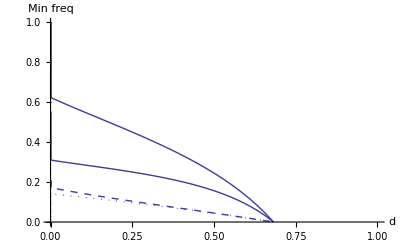

```mathematica
Show[
Plot[Total[unstableequil[d,1/2,0,1/2][[1]]],{d,0,1},PlotStyle->Thick,PlotRange->All],
Plot[unstableequil[d,1/2,0,1/2][[1,1]],{d,0,1},PlotStyle->Dashed],
Plot[unstableequil[d,1/2,0,1/2][[1,2]],{d,0,1},PlotStyle->Dotted],
Plot[unstableequil[d,1/2,0,1/2][[1,3]],{d,0,1}],
PlotRange->{{0,1},{0,1}},
AxesLabel->{"d","Min freq"}
]
```

r = 1/10:

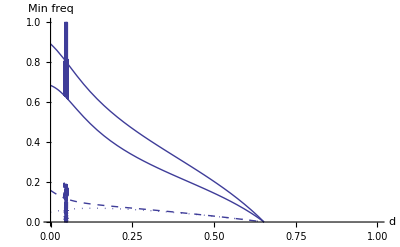

```mathematica
Show[
Plot[Total[unstableequil[d,1/2,0,1/10][[1]]],{d,0,1},PlotStyle->Thick,PlotRange->All],
Plot[unstableequil[d,1/2,0,1/10][[1,1]],{d,0,1},PlotStyle->Dashed,PlotRange->All],
Plot[unstableequil[d,1/2,0,1/10][[1,2]],{d,0,1},PlotStyle->Dotted,PlotRange->All],
Plot[unstableequil[d,1/2,0,1/10][[1,3]],{d,0,1},PlotRange->All],
PlotRange->{{0,1},{0,1}},
AxesLabel->{"d","Min freq"}
]
```

[I haven’t tried to fix the numerical glitches, but presumably they are coming from MachinePrecision being too low]

### APPROXIMATION - Assuming Ab and aB are dead-end gametes [Reasonable approximation for low thresholds]

We next assume that ϵ is near enough to zero that we can assume that Ab and aB do not contribute to the dynamics in any substantial way.  The easiest way to analyse the equations is then to pretend that the Ab and aB gametes are lethal:

```mathematica
newgametes*{1,0,0,1}//Simplify
```

{(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5])),0,0,-(r (-1+h s) (x[2] x[4]-x[1] x[5])+d^2 (-1+h s) (r x[2] x[4]+x[1] x[5]-r x[1] x[5])+d (-(-1+h s) x[2] (2 (-1+r) x[4]-x[5])+(2 r (-1+h s) x[1]+(-1+s) x[4]) x[5])+x[5] ((-1+h s) x[1]+(-1+h s) x[2]+(-1+s) (x[4]+x[5])))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))}

Then normalizing the equations:

```mathematica
(newgametes*{1,0,0,1})/Total[newgametes*{1,0,0,1}];
```

WARNING: Even though the next step in the life cycle is diploid selection and with ϵ=0, the above simplification is only an approximation because Ab and aB gametes are fine when paired with each other or with AB, as the toxin is neutralized.  Thus, this approach should work well as long as x[1] is common.

The last of these is the equation for the frequency of AB, and the change in AB frequency is expected to be:

```mathematica
Factor[Last[%]-x[5]/.x[2]->0/.x[4]->0/.x[1]->1-x[5]]
```

-((-1+x[5]) x[5] (-d^2+r-2 d r+d^2 r+h s+d^2 h s-h r s+2 d h r s-d^2 h r s-2 d x[5]+2 d^2 x[5]-2 r x[5]+4 d r x[5]-2 d^2 r x[5]+s x[5]-2 h s x[5]+2 d h s x[5]-2 d^2 h s x[5]+2 h r s x[5]-4 d h r s x[5]+2 d^2 h r s x[5]))/(-1+2 d x[5]-2 d^2 x[5]+2 r x[5]-4 d r x[5]+2 d^2 r x[5]+2 h s x[5]-2 d h s x[5]+2 d^2 h s x[5]-2 h r s x[5]+4 d h r s x[5]-2 d^2 h r s x[5]-2 d x[5]^2+2 d^2 x[5]^2-2 r x[5]^2+4 d r x[5]^2-2 d^2 r x[5]^2+s x[5]^2-2 h s x[5]^2+2 d h s x[5]^2-2 d^2 h s x[5]^2+2 h r s x[5]^2-4 d h r s x[5]^2+2 d^2 h r s x[5]^2)

This gives an approximate minimum value of x[5]:

```mathematica
Factor[Solve[%==0,x[5]]]
```

{{x[5]→0},{x[5]→1},{x[5]→(d^2-r+2 d r-d^2 r-h s-d^2 h s+h r s-2 d h r s+d^2 h r s)/(-2 d+2 d^2-2 r+4 d r-2 d^2 r+s-2 h s+2 d h s-2 d^2 h s+2 h r s-4 d h r s+2 d^2 h r s)}}

Rearranging critx (used Collect to help simplify):

```mathematica
critx=(d^2(1-h s)-h s-(1-d)^2 r (1-h s))/((1-2 h) s-2 d (1-d)(1-h s)-2 (1-d)^2 r (1-h s));
```

```mathematica
Factor[critx/.r->1/2]
```

(1-2 d-d^2+h s+2 d h s+d^2 h s)/(2 (1-d^2-s+h s+d^2 h s))

Plotting the critical value of x[5] above which invasion will occur for r=1/2:

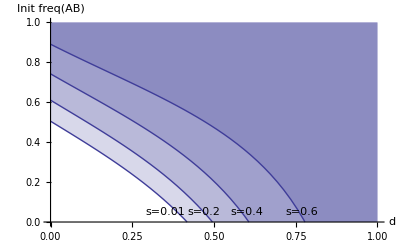

```mathematica
plot1=Show[
Plot[critx/.h->(1-√(1-s))/s/.r->1/2/.s->{0.01,0.2,0.4,0.6},{d,0,1},PlotRange->{Automatic,{0,1}},Filling->Top,AxesLabel->{"d","Init freq(AB)"}],
Graphics[Text["s=0.01",{0.35,0.05}]],
Graphics[Text["s=0.2",{0.47,0.05}]],
Graphics[Text["s=0.4",{0.6,0.05}]],
Graphics[Text["s=0.6",{0.77,0.05}]]
]
```

For r = 1/10:

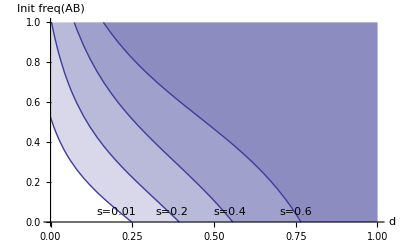

```mathematica
plot2=Show[
Plot[critx/.h->(1-√(1-s))/s/.r->1/10/.s->{0.01,0.2,0.4,0.6},{d,0,1},PlotRange->{Automatic,{0,1}},Filling->Top,AxesLabel->{"d","Init freq(AB)"}],
Graphics[Text["s=0.01",{0.2,0.05}]],
Graphics[Text["s=0.2",{0.37,0.05}]],
Graphics[Text["s=0.4",{0.55,0.05}]],
Graphics[Text["s=0.6",{0.75,0.05}]]
]
```

When these curves occur in regions of low x[5] (and d high), the curves are shifted to the left for r=1/10 relative to r=1/2, implying that invasion is easier to achieve for r small, which one would expect, especially when s is also small.

What is unexpected is that when these curves pass through high x[5] regions (and d low) then tighter linkage seems to be hurting.  This could be an an error in the approximation, but comparing it to the numerical solutions (below) suggests that it isn’t an artefact.  Rather for d small, the AB genotype is actually the lower of the two peaks when introducing AB into an ab population (having relative fitness & drive of (1+d^2) (1-h s)), and part of what gets the new AB haplotype into the population is that ab recombines with it and produces unfit Ab and aB haplotypes.

We can compare the above to the plots obtained by numerically solving for the equilibrium.  As the above only considers the introduction of AB, we use x[2]+x[4]+x[5] as the minimum amount of AB to introduce in the numerical solution.

r = 1/2:

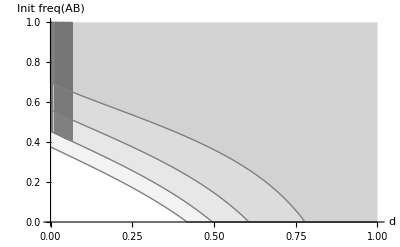

```mathematica
plot1b=Show[
Plot[Max[Total[unstableequil[d,0.01,0,1/2][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,AxesLabel->{"d","Init freq(AB)"},PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.2,0,1/2][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.4,0,1/2][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.6,0,1/2][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}]
]
```

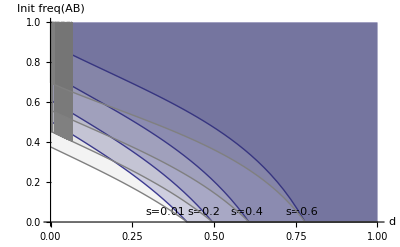

```mathematica
Show[plot1,plot1b]
```

r = 1/10:

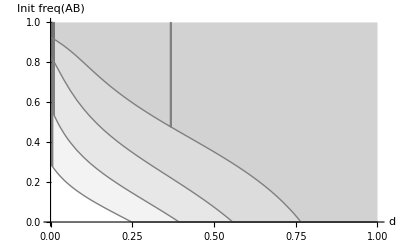

```mathematica
plot2b=Show[
Plot[Max[Total[unstableequil[d,0.01,0,1/10][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,AxesLabel->{"d","Init freq(AB)"},PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.2,0,1/10][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.4,0,1/10][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}],
Plot[Max[Total[unstableequil[d,0.6,0,1/10][[1]]],0],{d,0,1},PlotRange->{{0,1},{0,1}},Filling->Top,PlotStyle->Gray,FillingStyle->{GrayLevel[0.1,0.05]}]]
```

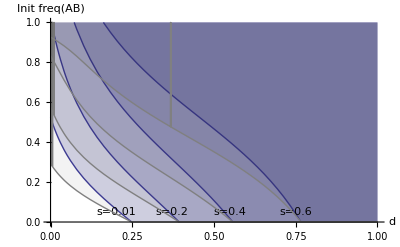

```mathematica
Show[plot2,plot2b]
```

In summary, critx=(d^2(1-h s)-h s-(1-d)^2 r (1-h s))/((1-2 h) s-2 d (1-d)(1-h s)-2 (1-d)^2 r (1-h s)) provides an excellent approximation for the minimum value of the AB haplotype that needs to be introduced when critx is small.  This makes sense because critx passes through x[5]=0 when invasion is possible at any initial frequency. But we established from the stability analysis that this occurs when r<critr, which is the same r value as obtained by solving critx=0 for r:

```mathematica
r/.Flatten[Solve[critx==0,r]]//Factor
```

(-d^2+h s+d^2 h s)/((-1+d)^2 (-1+h s))

```mathematica
r/.critr//Factor
```

(-d^2+h s+d^2 h s)/((-1+d)^2 (-1+h s))

However, critx=(d^2(1-h s)-h s-(1-d)^2 r (1-h s))/((1-2 h) s-2 d (1-d)(1-h s)-2 (1-d)^2 r (1-h s)) appears to overestimate the minimum threshold for AB genotypes when as that threshold rises towards one, as expected from the caveat mentioned above that the approximation considered here should fail most often when haplotypes may be paired with other haplotypes providing an antidote, which becomes increasingly likely as x[5] rises.

### APPROXIMATION - Assumes Ab and aB are equally frequent (s weak and ϵ ~ 0) [NOT USEFUL]

We can get the critical value assuming that s is small:

```mathematica
newgametes/.s->0//Simplify
```

{(x[1]^2+(-1+d)^2 r x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4])+(-1+d) (-1+r) x[5]))/(x[1]^2+2 x[2] x[4]+ϵ (x[2]^2+x[4]^2)+2 x[2] x[5]+2 x[4] x[5]+x[5]^2+2 x[1] (ϵ (x[2]+x[4])+x[5])),(ϵ x[2] ((1+d) x[1]+x[2])-(-1+d) ((d+r-d r) x[1] x[5]+x[2] ((1+(-1+d) r) x[4]+x[5])))/(x[1]^2+2 x[2] x[4]+ϵ (x[2]^2+x[4]^2)+2 x[2] x[5]+2 x[4] x[5]+x[5]^2+2 x[1] (ϵ (x[2]+x[4])+x[5])),(ϵ x[4] ((1+d) x[1]+x[4])-(-1+d) ((1+(-1+d) r) x[2] x[4]+(-d (-1+r) x[1]+r x[1]+x[4]) x[5]))/(x[1]^2+2 x[2] x[4]+ϵ (x[2]^2+x[4]^2)+2 x[2] x[5]+2 x[4] x[5]+x[5]^2+2 x[1] (ϵ (x[2]+x[4])+x[5])),(x[5] (x[1]+x[2]+x[4]+x[5])+r (x[2] x[4]-x[1] x[5])+d^2 (r x[2] x[4]+x[1] x[5]-r x[1] x[5])+d ((2 r x[1]+x[4]) x[5]+x[2] (-2 (-1+r) x[4]+x[5])))/(x[1]^2+2 x[2] x[4]+ϵ (x[2]^2+x[4]^2)+2 x[2] x[5]+2 x[4] x[5]+x[5]^2+2 x[1] (ϵ (x[2]+x[4])+x[5]))}

With s negligible, the system becomes symmetric (Ab and aB are equivalent).  If we assume that these two haplotypes are initially equally frequent, they should remain so:

```mathematica
Factor[newgametes[[2]]-newgametes[[3]]/.x[2]->x[4]/.s->0]
```

0

Assuming s=0 and that Ab and aB haplotypes are equally common, the equilibrium equations become:

```mathematica
equileqn=Factor[newgametes-{x[1],x[2],x[4],x[5]}/.x[1]->1-x[2]-x[4]-x[5]/.s->0/.x[4]->x[2]]//Numerator
```

{-2 x[2]+2 ϵ x[2]+2 d ϵ x[2]+10 x[2]^2-r x[2]^2+2 d r x[2]^2-d^2 r x[2]^2-10 ϵ x[2]^2-4 d ϵ x[2]^2-12 x[2]^3+12 ϵ x[2]^3+2 d x[5]-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]+6 x[2] x[5]-4 d x[2] x[5]+2 d^2 x[2] x[5]-2 r x[2] x[5]+4 d r x[2] x[5]-2 d^2 r x[2] x[5]-6 ϵ x[2] x[5]-2 d ϵ x[2] x[5]-14 x[2]^2 x[5]+14 ϵ x[2]^2 x[5]-2 d x[5]^2+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2-4 x[2] x[5]^2+4 ϵ x[2] x[5]^2,x[2]-ϵ x[2]-d ϵ x[2]-5 x[2]^2+d x[2]^2+r x[2]^2-2 d r x[2]^2+d^2 r x[2]^2+5 ϵ x[2]^2+2 d ϵ x[2]^2+6 x[2]^3-6 ϵ x[2]^3-d x[5]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]-x[2] x[5]+3 d x[2] x[5]-2 d^2 x[2] x[5]+2 r x[2] x[5]-4 d r x[2] x[5]+2 d^2 r x[2] x[5]+ϵ x[2] x[5]+d ϵ x[2] x[5]+4 x[2]^2 x[5]-4 ϵ x[2]^2 x[5]+d x[5]^2-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2,x[2]-ϵ x[2]-d ϵ x[2]-5 x[2]^2+d x[2]^2+r x[2]^2-2 d r x[2]^2+d^2 r x[2]^2+5 ϵ x[2]^2+2 d ϵ x[2]^2+6 x[2]^3-6 ϵ x[2]^3-d x[5]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]-x[2] x[5]+3 d x[2] x[5]-2 d^2 x[2] x[5]+2 r x[2] x[5]-4 d r x[2] x[5]+2 d^2 r x[2] x[5]+ϵ x[2] x[5]+d ϵ x[2] x[5]+4 x[2]^2 x[5]-4 ϵ x[2]^2 x[5]+d x[5]^2-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2,-2 d x[2]^2-r x[2]^2+2 d r x[2]^2-d^2 r x[2]^2-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]-4 x[2] x[5]-2 d x[2] x[5]+2 d^2 x[2] x[5]-2 r x[2] x[5]+4 d r x[2] x[5]-2 d^2 r x[2] x[5]+4 ϵ x[2] x[5]+6 x[2]^2 x[5]-6 ϵ x[2]^2 x[5]+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2+4 x[2] x[5]^2-4 ϵ x[2] x[5]^2}

The second and third of these requirements for an equilibrium are identical so we drop one.

```mathematica
equileqn[[2]]-equileqn[[3]]//Factor
```

0

```mathematica
equileqn=Drop[equileqn,{3}]
```

{-2 x[2]+2 ϵ x[2]+2 d ϵ x[2]+10 x[2]^2-r x[2]^2+2 d r x[2]^2-d^2 r x[2]^2-10 ϵ x[2]^2-4 d ϵ x[2]^2-12 x[2]^3+12 ϵ x[2]^3+2 d x[5]-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]+6 x[2] x[5]-4 d x[2] x[5]+2 d^2 x[2] x[5]-2 r x[2] x[5]+4 d r x[2] x[5]-2 d^2 r x[2] x[5]-6 ϵ x[2] x[5]-2 d ϵ x[2] x[5]-14 x[2]^2 x[5]+14 ϵ x[2]^2 x[5]-2 d x[5]^2+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2-4 x[2] x[5]^2+4 ϵ x[2] x[5]^2,x[2]-ϵ x[2]-d ϵ x[2]-5 x[2]^2+d x[2]^2+r x[2]^2-2 d r x[2]^2+d^2 r x[2]^2+5 ϵ x[2]^2+2 d ϵ x[2]^2+6 x[2]^3-6 ϵ x[2]^3-d x[5]+d^2 x[5]-r x[5]+2 d r x[5]-d^2 r x[5]-x[2] x[5]+3 d x[2] x[5]-2 d^2 x[2] x[5]+2 r x[2] x[5]-4 d r x[2] x[5]+2 d^2 r x[2] x[5]+ϵ x[2] x[5]+d ϵ x[2] x[5]+4 x[2]^2 x[5]-4 ϵ x[2]^2 x[5]+d x[5]^2-d^2 x[5]^2+r x[5]^2-2 d r x[5]^2+d^2 r x[5]^2,-2 d x[2]^2-r x[2]^2+2 d r x[2]^2-d^2 r x[2]^2-d^2 x[5]+r x[5]-2 d r x[5]+d^2 r x[5]-4 x[2] x[5]-2 d x[2] x[5]+2 d^2 x[2] x[5]-2 r x[2] x[5]+4 d r x[2] x[5]-2 d^2 r x[2] x[5]+4 ϵ x[2] x[5]+6 x[2]^2 x[5]-6 ϵ x[2]^2 x[5]+d^2 x[5]^2-r x[5]^2+2 d r x[5]^2-d^2 r x[5]^2+4 x[2] x[5]^2-4 ϵ x[2] x[5]^2}

```mathematica
Factor[Coefficient[equileqn[[1]],x[5]^2]equileqn[[3]]-Coefficient[equileqn[[3]],x[5]^2]equileqn[[1]]];
Flatten[Solve[%==0,x[5]]]//Simplify
```

{x[5]→(-d^3 (x[2]-2 r x[2]+(-1+r) ϵ (-1+2 x[2]))+(-1+ϵ) (r (1-5 x[2]+2 x[2]^2)+4 (-1+ϵ) x[2] (1-5 x[2]+6 x[2]^2))+d (-r (-2+ϵ+8 x[2]-8 ϵ x[2]-4 x[2]^2+4 ϵ x[2]^2)-4 (-1+ϵ) x[2] (x[2]+ϵ (-1+2 x[2])))+d^2 (1-3 x[2]+6 x[2]^2+ϵ (-1+5 x[2]-6 x[2]^2)+r (-1+x[2]-2 x[2]^2+ϵ (-1-x[2]+2 x[2]^2))))/(d^3 (-1+r) (-1+ϵ)-d^2 (1+ϵ+2 x[2]-2 ϵ x[2]+r (-1+ϵ) (1+2 x[2]))+d (-1+ϵ) (2 (3+2 ϵ) x[2]+r (-1+4 x[2]))-(-1+ϵ) (r (-1+2 x[2])+4 (-1+ϵ) x[2] (-1+4 x[2])))}

Making this substitution, we find that all the equilibrium equations are satisfied if and only if this quintic polynomial in  x[2]^5 is satisfied:

```mathematica
Factor[equileqn/.%]//Numerator;
```

```mathematica
quintic=(-2 d^4+d^5+2 d^2 r-6 d^3 r+6 d^4 r-2 d^5 r+d r^2-4 d^2 r^2+6 d^3 r^2-4 d^4 r^2+d^5 r^2+2 d^4 ϵ+d^5 ϵ-d^6 ϵ-2 d^2 r ϵ+4 d^3 r ϵ-4 d^5 r ϵ+2 d^6 r ϵ-d r^2 ϵ+3 d^2 r^2 ϵ-2 d^3 r^2 ϵ-2 d^4 r^2 ϵ+3 d^5 r^2 ϵ-d^6 r^2 ϵ-8 d^2 x[2]-4 d^3 x[2]+11 d^4 x[2]-2 d^5 x[2]-d^6 x[2]-16 d^2 r x[2]+37 d^3 r x[2]-23 d^4 r x[2]-d^5 r x[2]+3 d^6 r x[2]+r^2 x[2]-9 d r^2 x[2]+24 d^2 r^2 x[2]-26 d^3 r^2 x[2]+9 d^4 r^2 x[2]+3 d^5 r^2 x[2]-2 d^6 r^2 x[2]+16 d^2 ϵ x[2]+12 d^3 ϵ x[2]-14 d^4 ϵ x[2]-3 d^5 ϵ x[2]+3 d^6 ϵ x[2]+20 d^2 r ϵ x[2]-41 d^3 r ϵ x[2]+17 d^4 r ϵ x[2]+9 d^5 r ϵ x[2]-5 d^6 r ϵ x[2]-2 r^2 ϵ x[2]+12 d r^2 ϵ x[2]-26 d^2 r^2 ϵ x[2]+24 d^3 r^2 ϵ x[2]-6 d^4 r^2 ϵ x[2]-4 d^5 r^2 ϵ x[2]+2 d^6 r^2 ϵ x[2]-8 d^2 ϵ^2 x[2]-8 d^3 ϵ^2 x[2]+3 d^4 ϵ^2 x[2]+3 d^5 ϵ^2 x[2]-4 d^2 r ϵ^2 x[2]+4 d^3 r ϵ^2 x[2]+4 d^4 r ϵ^2 x[2]-4 d^5 r ϵ^2 x[2]+r^2 ϵ^2 x[2]-3 d r^2 ϵ^2 x[2]+2 d^2 r^2 ϵ^2 x[2]+2 d^3 r^2 ϵ^2 x[2]-3 d^4 r^2 ϵ^2 x[2]+d^5 r^2 ϵ^2 x[2]-16 d x[2]^2+34 d^2 x[2]^2-21 d^4 x[2]^2+6 d^5 x[2]^2+d^6 x[2]^2-2 r x[2]^2-4 d r x[2]^2+27 d^2 r x[2]^2-40 d^3 r x[2]^2+24 d^4 r x[2]^2-4 d^5 r x[2]^2-d^6 r x[2]^2-4 r^2 x[2]^2+14 d r^2 x[2]^2-17 d^2 r^2 x[2]^2+8 d^3 r^2 x[2]^2-2 d^4 r^2 x[2]^2+2 d^5 r^2 x[2]^2-d^6 r^2 x[2]^2+48 d ϵ x[2]^2-62 d^2 ϵ x[2]^2-16 d^3 ϵ x[2]^2+32 d^4 ϵ x[2]^2-2 d^6 ϵ x[2]^2+6 r ϵ x[2]^2+8 d r ϵ x[2]^2-58 d^2 r ϵ x[2]^2+66 d^3 r ϵ x[2]^2-20 d^4 r ϵ x[2]^2-2 d^5 r ϵ x[2]^2+8 r^2 ϵ x[2]^2-28 d r^2 ϵ x[2]^2+34 d^2 r^2 ϵ x[2]^2-16 d^3 r^2 ϵ x[2]^2+4 d^4 r^2 ϵ x[2]^2-4 d^5 r^2 ϵ x[2]^2+2 d^6 r^2 ϵ x[2]^2-48 d ϵ^2 x[2]^2+22 d^2 ϵ^2 x[2]^2+28 d^3 ϵ^2 x[2]^2-9 d^4 ϵ^2 x[2]^2-6 d^5 ϵ^2 x[2]^2-6 r ϵ^2 x[2]^2-4 d r ϵ^2 x[2]^2+35 d^2 r ϵ^2 x[2]^2-26 d^3 r ϵ^2 x[2]^2-6 d^4 r ϵ^2 x[2]^2+6 d^5 r ϵ^2 x[2]^2+d^6 r ϵ^2 x[2]^2-4 r^2 ϵ^2 x[2]^2+14 d r^2 ϵ^2 x[2]^2-17 d^2 r^2 ϵ^2 x[2]^2+8 d^3 r^2 ϵ^2 x[2]^2-2 d^4 r^2 ϵ^2 x[2]^2+2 d^5 r^2 ϵ^2 x[2]^2-d^6 r^2 ϵ^2 x[2]^2+16 d ϵ^3 x[2]^2+6 d^2 ϵ^3 x[2]^2-12 d^3 ϵ^3 x[2]^2-2 d^4 ϵ^3 x[2]^2+2 r ϵ^3 x[2]^2-4 d^2 r ϵ^3 x[2]^2+2 d^4 r ϵ^3 x[2]^2-8 x[2]^3+76 d x[2]^3-66 d^2 x[2]^3+18 d^4 x[2]^3-4 d^5 x[2]^3+2 r x[2]^3-2 d r x[2]^3-14 d^2 r x[2]^3+22 d^3 r x[2]^3-4 d^4 r x[2]^3-4 d^5 r x[2]^3-4 r^2 x[2]^3+16 d r^2 x[2]^3-24 d^2 r^2 x[2]^3+16 d^3 r^2 x[2]^3-4 d^4 r^2 x[2]^3+32 ϵ x[2]^3-228 d ϵ x[2]^3+150 d^2 ϵ x[2]^3+26 d^3 ϵ x[2]^3-32 d^4 ϵ x[2]^3-6 r ϵ x[2]^3-2 d r ϵ x[2]^3+38 d^2 r ϵ x[2]^3-38 d^3 r ϵ x[2]^3+8 d^5 r ϵ x[2]^3+8 r^2 ϵ x[2]^3-32 d r^2 ϵ x[2]^3+48 d^2 r^2 ϵ x[2]^3-32 d^3 r^2 ϵ x[2]^3+8 d^4 r^2 ϵ x[2]^3-48 ϵ^2 x[2]^3+228 d ϵ^2 x[2]^3-94 d^2 ϵ^2 x[2]^3-52 d^3 ϵ^2 x[2]^3+10 d^4 ϵ^2 x[2]^3+4 d^5 ϵ^2 x[2]^3+6 r ϵ^2 x[2]^3+10 d r ϵ^2 x[2]^3-34 d^2 r ϵ^2 x[2]^3+10 d^3 r ϵ^2 x[2]^3+12 d^4 r ϵ^2 x[2]^3-4 d^5 r ϵ^2 x[2]^3-4 r^2 ϵ^2 x[2]^3+16 d r^2 ϵ^2 x[2]^3-24 d^2 r^2 ϵ^2 x[2]^3+16 d^3 r^2 ϵ^2 x[2]^3-4 d^4 r^2 ϵ^2 x[2]^3+32 ϵ^3 x[2]^3-76 d ϵ^3 x[2]^3+2 d^2 ϵ^3 x[2]^3+26 d^3 ϵ^3 x[2]^3+4 d^4 ϵ^3 x[2]^3-2 r ϵ^3 x[2]^3-6 d r ϵ^3 x[2]^3+10 d^2 r ϵ^3 x[2]^3+6 d^3 r ϵ^3 x[2]^3-8 d^4 r ϵ^3 x[2]^3-8 ϵ^4 x[2]^3+8 d^2 ϵ^4 x[2]^3+40 x[2]^4-108 d x[2]^4+68 d^2 x[2]^4+8 d^3 x[2]^4-12 d^4 x[2]^4+8 r x[2]^4-28 d r x[2]^4+28 d^2 r x[2]^4-4 d^3 r x[2]^4-4 d^4 r x[2]^4-160 ϵ x[2]^4+348 d ϵ x[2]^4-184 d^2 ϵ x[2]^4-36 d^3 ϵ x[2]^4+24 d^4 ϵ x[2]^4-24 r ϵ x[2]^4+84 d r ϵ x[2]^4-88 d^2 r ϵ x[2]^4+20 d^3 r ϵ x[2]^4+8 d^4 r ϵ x[2]^4+240 ϵ^2 x[2]^4-396 d ϵ^2 x[2]^4+148 d^2 ϵ^2 x[2]^4+48 d^3 ϵ^2 x[2]^4-12 d^4 ϵ^2 x[2]^4+24 r ϵ^2 x[2]^4-84 d r ϵ^2 x[2]^4+92 d^2 r ϵ^2 x[2]^4-28 d^3 r ϵ^2 x[2]^4-4 d^4 r ϵ^2 x[2]^4-160 ϵ^3 x[2]^4+180 d ϵ^3 x[2]^4-16 d^2 ϵ^3 x[2]^4-20 d^3 ϵ^3 x[2]^4-8 r ϵ^3 x[2]^4+28 d r ϵ^3 x[2]^4-32 d^2 r ϵ^3 x[2]^4+12 d^3 r ϵ^3 x[2]^4+40 ϵ^4 x[2]^4-24 d ϵ^4 x[2]^4-16 d^2 ϵ^4 x[2]^4-48 x[2]^5+56 d x[2]^5-24 d^2 x[2]^5-8 r x[2]^5+16 d r x[2]^5-8 d^2 r x[2]^5+192 ϵ x[2]^5-216 d ϵ x[2]^5+72 d^2 ϵ x[2]^5+24 r ϵ x[2]^5-48 d r ϵ x[2]^5+24 d^2 r ϵ x[2]^5-288 ϵ^2 x[2]^5+312 d ϵ^2 x[2]^5-72 d^2 ϵ^2 x[2]^5-24 r ϵ^2 x[2]^5+48 d r ϵ^2 x[2]^5-24 d^2 r ϵ^2 x[2]^5+192 ϵ^3 x[2]^5-200 d ϵ^3 x[2]^5+24 d^2 ϵ^3 x[2]^5+8 r ϵ^3 x[2]^5-16 d r ϵ^3 x[2]^5+8 d^2 r ϵ^3 x[2]^5-48 ϵ^4 x[2]^5+48 d ϵ^4 x[2]^5);
```

```mathematica
Factor[%%/quintic]
```

{2 d-d^2+r-2 d r+d^2 r+4 x[2]-4 ϵ x[2],-(-1+d) (-d-r+d r),-d^2+r-2 d r+d^2 r-4 x[2]+4 ϵ x[2]}

Even the ϵ small case doesn’t provide much of an advantage (still quintic):

```mathematica
Factor[quintic/.ϵ->0]
```

-2 d^4+d^5+2 d^2 r-6 d^3 r+6 d^4 r-2 d^5 r+d r^2-4 d^2 r^2+6 d^3 r^2-4 d^4 r^2+d^5 r^2-8 d^2 x[2]-4 d^3 x[2]+11 d^4 x[2]-2 d^5 x[2]-d^6 x[2]-16 d^2 r x[2]+37 d^3 r x[2]-23 d^4 r x[2]-d^5 r x[2]+3 d^6 r x[2]+r^2 x[2]-9 d r^2 x[2]+24 d^2 r^2 x[2]-26 d^3 r^2 x[2]+9 d^4 r^2 x[2]+3 d^5 r^2 x[2]-2 d^6 r^2 x[2]-16 d x[2]^2+34 d^2 x[2]^2-21 d^4 x[2]^2+6 d^5 x[2]^2+d^6 x[2]^2-2 r x[2]^2-4 d r x[2]^2+27 d^2 r x[2]^2-40 d^3 r x[2]^2+24 d^4 r x[2]^2-4 d^5 r x[2]^2-d^6 r x[2]^2-4 r^2 x[2]^2+14 d r^2 x[2]^2-17 d^2 r^2 x[2]^2+8 d^3 r^2 x[2]^2-2 d^4 r^2 x[2]^2+2 d^5 r^2 x[2]^2-d^6 r^2 x[2]^2-8 x[2]^3+76 d x[2]^3-66 d^2 x[2]^3+18 d^4 x[2]^3-4 d^5 x[2]^3+2 r x[2]^3-2 d r x[2]^3-14 d^2 r x[2]^3+22 d^3 r x[2]^3-4 d^4 r x[2]^3-4 d^5 r x[2]^3-4 r^2 x[2]^3+16 d r^2 x[2]^3-24 d^2 r^2 x[2]^3+16 d^3 r^2 x[2]^3-4 d^4 r^2 x[2]^3+40 x[2]^4-108 d x[2]^4+68 d^2 x[2]^4+8 d^3 x[2]^4-12 d^4 x[2]^4+8 r x[2]^4-28 d r x[2]^4+28 d^2 r x[2]^4-4 d^3 r x[2]^4-4 d^4 r x[2]^4-48 x[2]^5+56 d x[2]^5-24 d^2 x[2]^5-8 r x[2]^5+16 d r x[2]^5-8 d^2 r x[2]^5

This could be numerically solved, but we already have a numerical procedure, and we don’t want to assume s small in general.

### Old (from Freek)

```mathematica
eq={(((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+√(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2))/(((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 √(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 (1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)^2),(ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+√(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+√(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2))/(((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 √(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 (1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)^2),(ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+√(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2))/(((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 √(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 (1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)^2),(√(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+√(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)^2)/(((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 ϵ ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))+ϵ ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2))^2+2 √(1-s) ((x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5])^2+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 √(1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])+(x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5])^2+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+2 (1-s) ((1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])^2+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)+(1-s) (2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5])+(1-d) (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1]^2+x[1] x[2]+x[1] x[4]+1/2 x[2] x[4]+1/2 x[1] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[2]+x[2]^2+1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1-d) (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+2 d (x[1] x[4]+1/2 x[2] x[4]+x[4]^2+1/2 x[1] x[5]+x[4] x[5]) (1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)+(1/2 x[2] x[4]+1/2 x[1] x[5]+x[2] x[5]+x[4] x[5]+x[5]^2)^2)^2)};
```